# SC-Magnon Coupling for Zigzag Ferromagnetic Nanoribbons

```mathematica
ClearAll["Global`*"]
```

## Functions

```mathematica
ZeroMatrix2N[N_]:=
Module[{N0=N,H},
H=Table[0,{2N0},{2N0}];
H
]

MZNRMatrix2N[J_,J2_,S_,DMI_,h_,κ_,Δκ_,ξ_,ϕ_,Num_]:=
Module[{H,N0=Num},
H=ZeroMatrix2N[N0];

(*Note that the Quiet[] is there so that the code doesn't throw any errors 
about trying to define matrix elements with indices greater than 2N*)
Quiet[
Do[
H[[i,i+1]]=-J S((E^(ⅈ ξ√3 /2)+Conjugate[E^(ⅈ ξ √3/2)] )(1/2+(-1)^(i-1)1/2)+(1/2+(-1)^i 1/2));
H[[i+1,i]]=Conjugate[H[[i,i+1]]];
H[[i,i+2]]=-√(DMI^2+J2^2)S (E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)+Conjugate[E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)]);
H[[i+2,i]]=Conjugate[H[[i,i+2]]];
H[[i,i]]=3J S+6J2 S+h+κ-√(DMI^2+J2^2) S (E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)+Conjugate[E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)])+(-1)^(i-1)Δκ S;
,{i,1,2N0}];
];
(*Onsite edge effects*)
H[[1,1]]=H[[1,1]]-J S-2J2 S;
H[[2,2]]=H[[2,2]]-2J2 S;
H[[2N0-1,2N0-1]]=H[[2N0-1,2N0-1]]-2J2 S;
H[[2N0,2N0]]=H[[2N0,2N0]]-J S-2J2 S;
H
]



DyadG[x_,y_,z_,x1_,y1_,z1_]:=
Module[{DG,G},
DG=({{-(3 (x-x1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)), -(3 (x-x1) (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))}, {-(3 (x-x1) (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (y-y1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)), -(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))}, {-(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), 1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))-(3 (z-z1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))}});
DG
]

UMatrix[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=MZNRMatrix2N[J1,J2,s,DM,h,κ,Δκ,ξ,ϕ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]

(*MZNRCouplingDiscrete[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
y1=3/2 M;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=(√3 3)/4 Norm[NIntegrate[Sum[(Chop[U[[m]]][[M]](1+(-1)^(M-1))/2 E^(ⅈ ξ Mod[x,(√3)/2])+E^(ⅈ ξ ((√3)/2-Mod[x,(√3)/2]))Chop[U[[m]]][[M]](1+(-1)^M)/2)(A[[1]][[1]]-A[[2]][[2]])E^(ⅈ ξ x1),{x1,sum1,sum2,√3},{M,1,2N}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];
Chop[g,10^-10]
]*)


MZNRCouplingDiscrete[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
y1=RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2N}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N];
g=(√3 3)/4 Norm[NIntegrate[Sum[(U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(ⅈ ξ ((√3)/2))U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(ⅈ ξ ((√3)/2))U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*((3 (-y1[[M]]+y)^2)/(((-x1+x)^2+(-y1[[M]]+y)^2+(-z1+z)^2)^(5/2))-(3 (-x1+x)^2)/(((-x1+x)^2+(-y1[[M]]+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ x1),{x1,sum1,sum2,√3},{M,1,2N}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

(*Assumes x>0*)
Chop[g,10^-10]
]

(*MZNRCouplingContinuous[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,int1_,int2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
y1=3/2 M;
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[U[[m]][[M]]*(A[[1]][[1]]-A[[2]][[2]]),{M,1,2N}] 3/2 E^(ⅈ ξ x1),{x1,int1,int2},{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];
g
]*)

(*(*Takes a table of two component lists and creates a smooth function*)
InterpolateIt[List_,lb_,ub_]:=
Module[{EmptyList,v},
EmptyList={};
Do[
AppendTo[EmptyList,List[[j]][[2]]]
,{j,1,Length[List]}];
v=ListInterpolation[EmptyList,{lb,ub}];
v
]*)

MZNRStrayField[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
y1=RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2N}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N];

g=(√3 3)/4 NIntegrate[Sum[(U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(ⅈ ξ ((√3)/2))U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(ⅈ ξ ((√3)/2))U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*((3 (-y1[[M]]+y)^2)/(((-x1+x)^2+(-y1[[M]]+y)^2+(-z1+z)^2)^(5/2))+(3 (-x1+x)^2)/(((-x1+x)^2+(-y1[[M]]+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ x1),{x1,sum1,sum2,√3},{M,1,2N}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}];

{g+Conjugate[g],ⅈ*(g-Conjugate[g])}
]
```

### Impurity Functions

```mathematica
ImpureMZNRMatrix2N[J_,J2_,S_,DMI_,h_,κ_,ξ_,ϕ_,Num_]:=
Module[{H,N0=Num,N00},
H=ZeroMatrix2N[N0];

(*Note that the Quiet[] is there so that the code doesn't throw any errors 
about trying to define matrix elements with indices greater than 2N*)
Quiet[
Do[
H[[i,i+1]]=-J S((E^(ⅈ ξ√3 /2)+Conjugate[E^(ⅈ ξ √3/2)] )(1/2+(-1)^(i-1)1/2)+(1/2+(-1)^i 1/2));
H[[i+1,i]]=Conjugate[H[[i,i+1]]];
H[[i,i+2]]=-√(DMI^2+J2^2)S (E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)+Conjugate[E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)]);
H[[i+2,i]]=Conjugate[H[[i,i+2]]];
H[[i,i]]=3J S+6J2 S+h-√(DMI^2+J2^2) S (E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)+Conjugate[E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)])+(-1)^(i-1)κ;
,{i,1,2N0}];
];
(*Onsite edge effects*)
H[[1,1]]=H[[1,1]]-J S-2J2 S;
H[[2,2]]=H[[2,2]]-2J2 S;
H[[2N0-1,2N0-1]]=H[[2N0-1,2N0-1]]-2J2 S;
H[[2N0,2N0]]=H[[2N0,2N0]]-J S-2J2 S;

N00=N0-2;

(*Onsite A Sublattice Effects*)
H[[N00-3,N00-3]]=H[[N00-3,N00-3]]-4J2 S;
H[[N00-1,N00-1]]=0;

(*Onsite B Sublattice Effects*)
H[[N00-2,N00-2]]=H[[N00-2,N00-2]]-J S;
H[[N00,N00]]=H[[N00,N00]]-2J S;

(*NN Effects*)
H[[N00,N00-1]]=0;
H[[N00-1,N00]]=0;
H[[N00-1,N00-2]]=0;
H[[N00-2,N00-1]]=0;

(*NNN Effects*)
H[[N00-1,N00-3]]=0;
H[[N00-3,N00-1]]=0;
H[[N00+1,N00-1]]=0;
H[[N00-1,N00+1]]=0;

H
]

MZNRMatrix2NBImpure[J_,J2_,S_,DMI_,h_,κ_,ξ_,ϕ_,Num_]:=
Module[{H,N0=Num,N00},
H=ZeroMatrix2N[N0];

(*Note that the Quiet[] is there so that the code doesn't throw any errors 
about trying to define matrix elements with indices greater than 2N*)
Quiet[
Do[
H[[i,i+1]]=-J S((E^(ⅈ ξ√3 /2)+Conjugate[E^(ⅈ ξ √3/2)] )(1/2+(-1)^(i-1)1/2)+(1/2+(-1)^i 1/2));
H[[i+1,i]]=Conjugate[H[[i,i+1]]];
H[[i,i+2]]=-√(DMI^2+J2^2)S (E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)+Conjugate[E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)]);
H[[i+2,i]]=Conjugate[H[[i,i+2]]];
H[[i,i]]=3J S+6J2 S+h-√(DMI^2+J2^2) S (E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)+Conjugate[E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)])+(-1)^(i-1)κ;
,{i,1,2N0}];
];
(*Onsite edge effects*)
H[[1,1]]=H[[1,1]]-J S-2J2 S;
H[[2,2]]=H[[2,2]]-2J2 S;
H[[2N0-1,2N0-1]]=H[[2N0-1,2N0-1]]-2J2 S;
H[[2N0,2N0]]=H[[2N0,2N0]]-J S-2J2 S;

N00=N0;

(*(*Onsite A Sublattice Effects*)
H[[N00-3,N00-3]]=H[[N00-3,N00-3]]-4J2 S;
H[[N00-1,N00-1]]=0;

(*Onsite B Sublattice Effects*)
H[[N00-2,N00-2]]=H[[N00-2,N00-2]]-J S;
H[[N00,N00]]=H[[N00,N00]]-2J S;*)

(*NN Effects*)
H[[N00,N00-1]]=0;
H[[N00-1,N00]]=0;
H[[N00-1,N00-2]]=0;
H[[N00-2,N00-1]]=0;

(*NNN Effects*)
H[[N00-1,N00-3]]=0;
H[[N00-3,N00-1]]=0;
H[[N00+1,N00-1]]=0;
H[[N00-1,N00+1]]=0;

H
]

ImpureUMatrix[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=ImpureMZNRMatrix2N[J1,J2,s,DM,h,κ,ξ,ϕ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]

ImpureUMatrixB[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=MZNRMatrix2NBImpure[J1,J2,s,DM,h,κ,ξ,ϕ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]
```

### Test Functions

```mathematica
MZNRCouplingTest[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
z1=0;
y1=3/2 M;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=(√3 3)/4 Norm[NIntegrate[Sum[(Chop[U[[m]]][[M]](1+(-1)^(M-1))/2 E^(ⅈ ξ Mod[x,(√3)/2])+E^(ⅈ ξ ((√3)/2-Mod[x,(√3)/2]))Chop[U[[m]]][[M]](1+(-1)^M)/2)(A[[1]][[1]]-A[[2]][[2]])E^(ⅈ ξ x1),{x1,-√3*1000,√3*1000,√3},{M,1,2N}],{z1,-1/4,0},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
(*Chop[g,10^-10]*)
g
]

MZNRCouplingDiscreteTest[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
y1=RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2N}];
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=(√3 3)/4 Norm[NIntegrate[Sum[(U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(ⅈ ξ ((√3)/2))U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(ⅈ ξ ((√3)/2))U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*((3 (-y1[[M]]+y)^2)/(((-x1+x)^2+(-y1[[M]]+y)^2+(-z1+z)^2)^(5/2))-(3 (-x1+x)^2)/(((-x1+x)^2+(-y1[[M]]+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ x1),{x1,sum1,sum2,√3},{M,1,2N}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

(*Assumes x>0*)
Chop[g,10^-10]
]


MZNRCouplingContinuousTest[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,int1_,int2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
y1=3M;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[(U[[m]][[4M-3]]+U[[m]][[4M-2]]+U[[m]][[4M-1]]+U[[m]][[4M]])/4*((3 (-y1+y)^2)/((-x1+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)-(3 (-x1+x)^2)/((-x1+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)),{M,1,N/2}]3 E^(ⅈ ξ x1),{x1,int1,int2},{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];
g
]

(*MZNRCouplingTest2[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
y1=3/2 M;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=Norm[Sum[NIntegrate[U[[m]][[M]]*(A[[1]][[1]]-A[[2]][[2]])3/2 E^(ⅈ ξ x1),{x1,-√3100,√3 100},{z1,-1,0},Method->{Automatic,"SymbolicProcessing"->0}],{M,1,2N}]];
g
]*)
```

## MZNR Lattice

```mathematica
av={3/2,√3/2};
bv={3/2,-√3/2};
cv=-(bv+av)/3;
δ={cv,(-av+2bv)/3,{1/2,√3/2}};
α={av,-bv,-(av-bv)};
```

```mathematica
LatticeA[n_,m_]:=n av.RotationMatrix[-Pi/6] +m bv.RotationMatrix[-Pi/6];
LatticeB[n_,m_]:=n av.RotationMatrix[-Pi/6] +m bv.RotationMatrix[-Pi/6]+Indexed[δ,2].RotationMatrix[-Pi/6];
A=ListPlot[Table[LatticeA[n,m],{n,-5,6,1},{m,-10,10,1}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{},PlotStyle->{Darker[Cyan]},PlotTheme->"Scientific",PlotMarkers->Graphics[Disk[],ImageSize->5],PlotRange->All,ImageSize->Large];
B=ListPlot[Table[LatticeB[n,m],{n,-5,6,1},{m,-10,10,1}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{},PlotStyle->{Darker[Red]},PlotTheme->"Scientific",PlotMarkers->Graphics[Disk[],ImageSize->5],PlotRange->All,ImageSize->Large];
LeftSpat=
c=ListPlot[Table[LatticeA[0,m],(*{n,-5,5,1},*){m,-10,10,1}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{},PlotStyle->{Black},PlotTheme->"Scientific",PlotMarkers->{"X",Small},PlotRange->All,ImageSize->Large];

δvec=Graphics[Arrow[{{0,0},Indexed[δ,1].RotationMatrix[-Pi/6]}],Small];
Avec=Graphics[Arrow[{{0,0},av.RotationMatrix[-Pi/6]}],Small];
Bvec=Graphics[Arrow[{{0,0},bv.RotationMatrix[-Pi/6]}],Small];
(*UCL=Graphics[Line[{LatticeA[-5,0]-{0,1},LatticeA[7,0]-{0,1}}]];
UCR=Graphics[Line[{LatticeA[-7,0]+{0,2},LatticeA[5,0]+{0,2}}]];*)
UCL=Graphics[Line[{{-Sqrt[3]/4,-9},{-Sqrt[3]/4,10}}]];
UCR=Graphics[Line[{{(3 Sqrt[3])/4,-9},{(3 Sqrt[3])/4,10}}]];
```

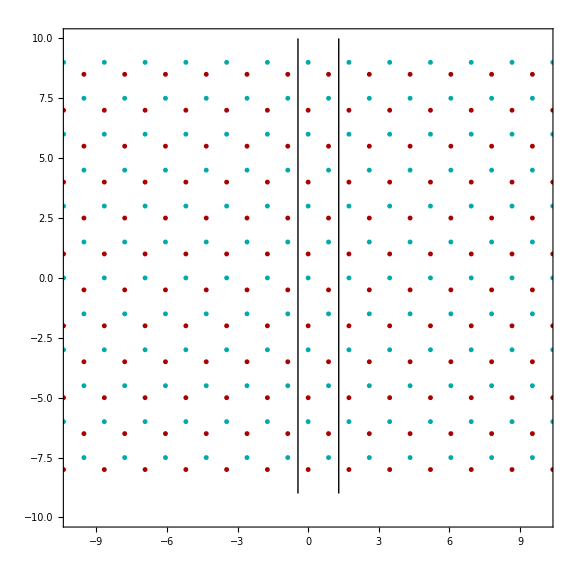

```mathematica
Show[{A,B,UCL,UCR(*,δvec,Avec,Bvec*)},PlotRange->(*Full*){{-10,10},{-10,10}},AspectRatio->1,GridLines->{{},{}}]
```

```mathematica
Export["C:\\Users\\jeffc\\Downloads\\MZNR-Unit_cell.png",%737,"PNG"]
```

C:\Users\jeffc\Downloads\MZNR-Unit_cell.png

```mathematica
k=MeanMom[2.7,0.01][[1]][[2]];
band=MeanMom[2.7,0.01][[1]][[1]];
```

```mathematica
U=Abs[UMatrix[J,J2,DM,s,κ,h,ϕ,k,Num][[band]]]^2
```

{2.80128×10^-13,9.3498×10^-13,1.33982×10^-12,3.93317×10^-12,1.09408×10^-11,2.27836×10^-11,7.41101×10^-11,1.45368×10^-10,4.85302×10^-10,9.43032×10^-10,3.16102×10^-9,6.13356×10^-9,2.05724×10^-8,3.99092×10^-8,1.33871×10^-7,2.59693×10^-7,8.71123×10^-7,1.68986×10^-6,5.66849×10^-6,0.000010996,0.0000368839,0.0000715453,0.000239944,0.000465309,0.00155909,0.00301931,0.0100676,0.0193552,0.0628727,0.116149,0.324289,0.461854}

```mathematica
MeanMom[2.7,0.01]
```

{{17,1.14269,2.70241},{17,-1.14269,2.70241}}

## Parameter Definitions

### Lattice Parameters

```mathematica
a=4*10^-10(*m*);
J=2;
h=0.05;
J2=0.15;
s=3/2;
DM=0.3;
κ=0;
ϕ=ArcTan[DM/J2];
ℏ=6.582*10^-1; (*meV/THz*)
```

### Constants

```mathematica
kb=8.6*10^-2; (*meV*)

γe=1.76*10^11;(*rad*s^-1*T^-1*)
μ0=4Pi*10^-7;(*N/m^2*)
μB=9.274*10^-24 (*J*T^-1*);
Ms=(3/2 μB s)/(a^2 w);
w=10^-10;(*m*)
```

### Computational Settings

```mathematica
WP=60;
AG=10;
```

## MZNR Dispersion

```mathematica
Naux=300;
Num=30;
κ=0;

Do[
ξ=-Pi/(√3)+j* N[((2Pi)/(√3))/Naux];

H=MZNRMatrix2N[J,J2,s,DM,h,κ,ξ,ϕ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,Eigensystem[H][[1]][[sortorder]][[i]] 1/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]

RightUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>0&];
RightLowerBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>0&];
LeftUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<0&];
LeftLowerBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<0&];
PositiveBand=Select[Join[LeftUpperBand,RightLowerBand],1.8<#[[2]]<3.4&];
NegativeBand=Select[Join[LeftLowerBand,RightUpperBand],1.8<#[[2]]<3.4&];
```

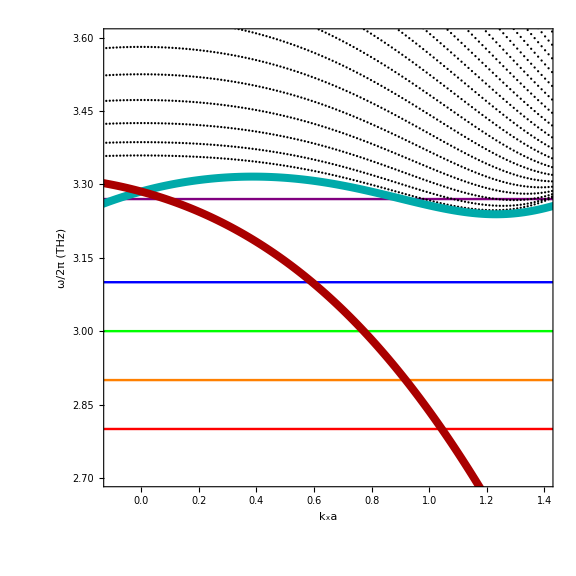

```mathematica
p=ListPlot[Table[f[ξ],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"k_xa","ω/2π (THz)"},PlotStyle->Directive[Black,Thickness[.1]],PlotRange->All,PlotTheme->"Scientific",GridLines->{{},{2.2,3.2}}];
ppos=ListPlot[PositiveBand,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Darker[Cyan],Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",Joined->True];
pneg=ListPlot[NegativeBand,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Darker[Red],Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",Joined->True];
Show[{p,ppos,pneg},PlotRange->{{-0.1,1.4},{2.7,3.6}},ImageSize->Large,GridLines->{{},{{2.8,Red},{2.9,Orange},{3,Green},{3.1,Blue},{3.27,Purple}}},GridLinesStyle->Directive[Thickness[.003]],AspectRatio->1]
```

### Pretty Picture

```mathematica
Naux=500;
Num=30;
κ=0;
Δκ=0;
J2=0;
DM=0;

Do[
ξ=-Pi/(√3)+j* N[((2Pi)/(√3))/Naux];

H=MZNRMatrix2N[J,J2,s,DM,h,κ,Δκ,ξ,ϕ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,Eigensystem[H][[1]][[sortorder]][[i]] 1/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]

(*RightUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>Pi/(√3)&];
RightLowerBand=Select[Table[f[ξ][[Num+2]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>Pi/(√3)&];
LeftUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<Pi/(√3)&];
LeftLowerBand=Select[Table[f[ξ][[Num+2]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<Pi/(√3)&];

LeftLowerLowerBand=Select[Table[f[ξ][[Num]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<Pi/(√3)&];
LeftUpperUpperBand=Select[Table[f[ξ][[Num+3]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<Pi/(√3)&];
RightLowerLowerBand=Select[Table[f[ξ][[Num]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>Pi/(√3)&];
RightUpperUpperBand=Select[Table[f[ξ][[Num+3]],{ξ,0,(2Pi)/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>Pi/(√3)&];*)

RightUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>0&];
RightLowerBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>0&];
LeftUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<0&];
LeftLowerBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<0&];

LeftLowerLowerBand=Select[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<0&];
LeftUpperUpperBand=Select[Table[f[ξ][[Num+3]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]<0&];
RightLowerLowerBand=Select[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>0&];
RightUpperUpperBand=Select[Table[f[ξ][[Num+3]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],#[[1]]>0&];

PositiveBand=Select[Join[LeftUpperBand,RightLowerBand,RightLowerLowerBand],1.7<#[[2]]<3.5&];
NegativeBand=Select[Join[LeftLowerBand,RightUpperBand,LeftLowerLowerBand],1.7<#[[2]]<3.5&];
```

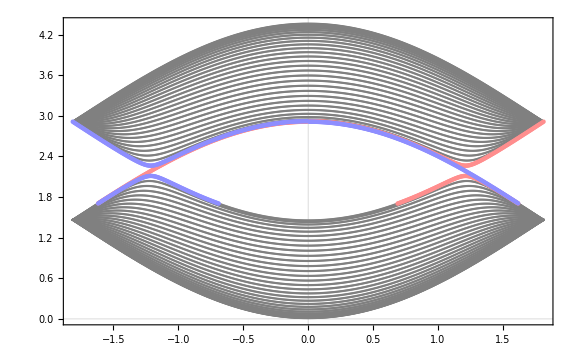

```mathematica
p=ListPlot[Table[f[ξ],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"k_xa","ω/2π (THz)"},FrameStyle->Thick,PlotStyle->Directive[Gray,Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"(*,GridLines->{{Pi/(√3)},{}}*)];
ppos=ListPlot[PositiveBand,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->48}],FrameLabel->{"k_ya","ω/2π (THz)"},PlotStyle->Directive[Lighter[Lighter[Red]](*RGBColor["#cc5c57"]*),FrameStyle->Thick,Thickness[.01]],PlotRange->All(*,PlotMarkers->{"●",Small}*),PlotTheme->"Scientific"];
pneg=ListPlot[NegativeBand,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->48}],FrameLabel->{"k_ya","ω/2π (THz)"},FrameStyle->Thick,PlotStyle->Directive[Lighter[Lighter[Blue]](*RGBColor["#399283"]*),Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"(*,PlotMarkers->{"●",Small}*)];
Show[{p,ppos,pneg},ImageSize->Large,(*GridLines->{{},{{2.2,Directive[RGBColor["#ada132"],Thickness[0.008],Opacity[0.75]]},{2.7,Directive[RGBColor["#789953"],Thickness[0.008],Opacity[0.75]]},{3.2,Directive[RGBColor["#9f6dbe"],Thickness[0.008],Opacity[0.75]]}}},Method->{"GridLinesInFront"->True},*)(*GridLines->{{},{3.1+κ/(2Pi ℏ)}},*)(*GridLinesStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.0075]],*)FrameStyle->Directive[Thick,Ticks->{-1,0,1}],FrameLabel->{}]
```

{0.430739,Null}

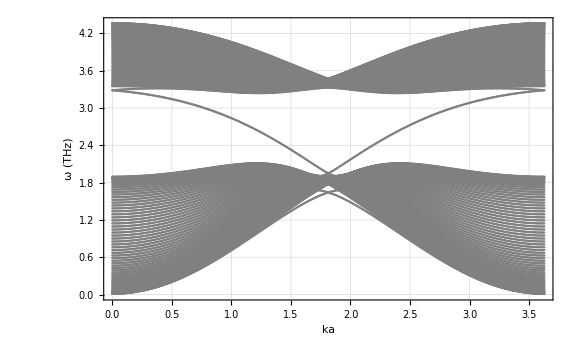

```mathematica
NSamp = 500; (*Number of sample points*)
Num=59; (*Half the number of bands*)
Δκ=0; (*Difference in easy-axis anisotropy*)

f[ξ_]:=
Module[{H,sortorder,dumH},
H=MZNRMatrix2N[J,J2,s,DM,h,0,Δκ,ξ,ϕ,Num];
dumH=Eigenvalues[H];(*eigenvalues*)
sortorder=Ordering[dumH];(*This orders the eigenvalues and eigenfunctions accordingly*)

Table[{ξ ,(dumH[[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}]
]

Dispersion = ParallelMap[f,Table[j* N[(2 Pi/(√3))/NSamp],{j,0,NSamp}]];//AbsoluteTiming

ListPlot[Dispersion,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Gray,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{}]
```

## MZNR Wavefunctions

### For a Given Range

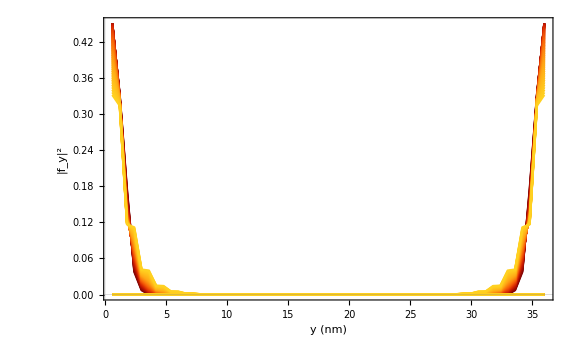

```mathematica
(*Plot range of wavefunctions given some dispersion range*)
Wavefunctions={};
Do[
U1=UMatrix[J,J2,DM,s,κ,h,ϕ,PositiveBand[[j]][[1]],Num];
fl=Table[{3/2 M *a/10^-9,Abs[U1[[Num+1]][[M]]]^2},{M,0,2Num}];
U2=UMatrix[J,J2,DM,s,κ,h,ϕ,Reverse[NegativeBand][[j]][[1]],Num];
fr=Table[{3/2 M a/10^-9,Abs[U2[[Num+1]][[M]]]^2},{M,0,2Num}];
AppendTo[Wavefunctions,{fl,fr}]
,{j,1,Length[PositiveBand]}]

Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->True,PlotStyle->ColorData["SolarColors",j/Length[Wavefunctions]],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|f_y|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All]
```

### Wavefunction Algorithm

```mathematica
(*Calculate table of values*)
(*κ=0.3;
Δκ=0.05;*)

Naux=500;
Num=34;

upperbound=3.4;
lowerbound=1.8;

WaveAlgo[J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A},

(*diagonalizes hamiltonian eigensystem*)
Do[
ξ=-Pi/(√3)+j* N[(2 Pi/(√3))/Naux];

H=MZNRMatrix2N[J,J2,s,DM,h,κ,Δκ,ξ,ϕ,Num];
A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/NBand]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/NBand]}]]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for spin lattice*)
wavefunctions[ω_,err_,N0]:=
Module[{wavefunction,U,f,k,band,β,n,y},
wavefunction={};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=UMatrix[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
y=RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{y[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMom[ω,err]]}];

wavefunction

];

];
```

### Plot spatial profiles

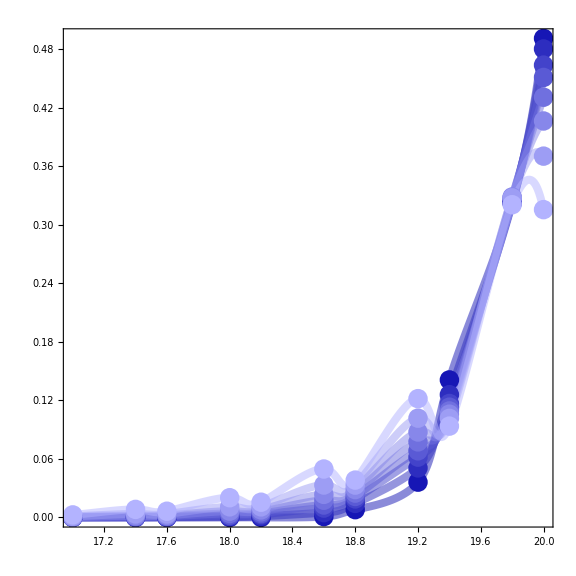

```mathematica
(*run wavealgo anytime you initialize kernel or update a variable*)
(*WaveAlgo[J,J2,DM,s,κ,0,h,ϕ,Num,100,upperbound,lowerbound];

(*Colors={Red,Orange,Green,Blue,Purple,Magenta};*)

(*wavecolors={{RGBColor["#e6a835"],RGBColor["#07f738"]},{RGBColor["#eaa23a"],RGBColor["#0aeb5a"]},{RGBColor["#e69037"],RGBColor["#07f78a"]},{RGBColor["#e57e36"],RGBColor["#0beba9"]},{RGBColor["#e67137"],RGBColor["#07f7db"]},{RGBColor["#f56438"],RGBColor["#08d9db"]},{RGBColor["#e65337"],RGBColor["#07c6f7"]},{RGBColor["#e63741"],RGBColor["#0584c7"]},{RGBColor["#ad352c"],RGBColor["#077af7"]}};*)

Wavefunctions=ConstantArray[0,11];

Do[
ω=2.2+0.1*(j-1);
Wavefunctions[[j]]=wavefunctions[ω,1/100,Num]
,{j,1,11}];*)

test1=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[2]][[;;20]],PlotRange->All,Joined->False,PlotMarkers->{"●",Medium},PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];
test2=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[2]][[;;20]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_m(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];

test3=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[1]][[48;;]],PlotRange->All,Joined->False,PlotMarkers->{"●",Large},PlotStyle->Directive[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];
test4=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[1]][[48;;]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Opacity[0.5],Thickness[0.01]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];

ColorList=Table[Blend[{Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},1],White,Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},1]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]]]],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]]]}];

test5=Table[ListPlot[{Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]][[j]]},PlotRange->All,Joined->False,PlotMarkers->{"●",Medium},PlotStyle->Directive[ColorList[[j]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]]]}];

test6=Table[ListPlot[Partition[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]],2][[j]],Joined->True,PlotRange->All,Joined->True,
PlotStyle->Directive[ColorList[[2j]],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[Partition[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]],2]]}];

(*Show[test2,test1,test4,test3,test6,test5,FrameStyle->Directive[Thickness[0.007],FontSize->36],GridLines->{},AspectRatio->3/4,FrameLabel->{}]*)
Show[test4,test3,FrameStyle->Directive[Thickness[0.01],FontSize->48],GridLines->{},AspectRatio->1,FrameLabel->{},PlotRange->{{17,20},All}]
```

```mathematica
gradient[pos_->colors_]:=Graphics[{LinearGradientFilling[pos->colors],Polygon[{{0,0},{1,0},{1,1},{0,1}}]}(*GridLines->{Thread[{pos,colors}],None}*),GridLinesStyle->Thick,AspectRatio->.1];
gradient[Table[j/8,{j,0,8}]->Table[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],{j,0,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}]]
gradient[Table[j/8,{j,0,8}]->Table[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],{j,0,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}]]
```

-Graphics-

-Graphics-

```mathematica
Wavefunctions[[11]]
```

{{{0,1.80669×10^-13},{1/5,2.70979×10^-13},{3/5,1.4279×10^-13},{4/5,2.39949×10^-13},{6/5,2.83093×10^-13},{7/5,3.22169×10^-13},{9/5,6.31172×10^-13},{2,5.80308×10^-13},{12/5,1.4882×10^-12},{13/5,1.23722×10^-12},{3,3.59384×10^-12},{16/5,2.85983×10^-12},{18/5,8.76533×10^-12},{19/5,6.84856×10^-12},{21/5,2.14659×10^-11},{22/5,1.66459×10^-11},{24/5,5.26569×10^-11},{5,4.07073×10^-11},{27/5,1.29258×10^-10},{28/5,9.97989×10^-11},{6,3.17378×10^-10},{31/5,2.4492×10^-10},{33/5,7.79375×10^-10},{34/5,6.01316×10^-10},{36/5,1.91398×10^-9},{37/5,1.47658×10^-9},{39/5,4.70039×10^-9},{8,3.62609×10^-9},{42/5,1.15434×10^-8},{43/5,8.90499×10^-9},{9,2.8349×10^-8},{46/5,2.18692×10^-8},{48/5,6.96211×10^-8},{49/5,5.37076×10^-8},{51/5,1.7098×10^-7},{52/5,1.31898×10^-7},{54/5,4.19901×10^-7},{11,3.23923×10^-7},{57/5,1.03122×10^-6},{58/5,7.95509×10^-7},{12,2.53253×10^-6},{61/5,1.95366×10^-6},{63/5,6.21953×10^-6},{64/5,4.79791×10^-6},{66/5,0.0000152743},{67/5,0.000011783},{69/5,0.0000375115},{14,0.0000289373},{72/5,0.0000921229},{73/5,0.000071066},{15,0.000226241},{76/5,0.000174528},{78/5,0.000555616},{79/5,0.000428616},{81/5,0.00136451},{82/5,0.00105262},{84/5,0.00335105},{17,0.00258509},{87/5,0.00822972},{88/5,0.00634861},{18,0.020211},{91/5,0.0155913},{93/5,0.049636},{94/5,0.0382921},{96/5,0.121791},{97/5,0.0936383},{99/5,0.320637},{20,0.315611}},{{0,0.315611},{1/5,0.320637},{3/5,0.0936383},{4/5,0.121791},{6/5,0.0382921},{7/5,0.049636},{9/5,0.0155913},{2,0.020211},{12/5,0.00634861},{13/5,0.00822972},{3,0.00258509},{16/5,0.00335105},{18/5,0.00105262},{19/5,0.00136451},{21/5,0.000428616},{22/5,0.000555616},{24/5,0.000174528},{5,0.000226241},{27/5,0.000071066},{28/5,0.0000921229},{6,0.0000289373},{31/5,0.0000375115},{33/5,0.000011783},{34/5,0.0000152743},{36/5,4.79791×10^-6},{37/5,6.21953×10^-6},{39/5,1.95366×10^-6},{8,2.53253×10^-6},{42/5,7.95509×10^-7},{43/5,1.03122×10^-6},{9,3.23923×10^-7},{46/5,4.19901×10^-7},{48/5,1.31898×10^-7},{49/5,1.7098×10^-7},{51/5,5.37076×10^-8},{52/5,6.96211×10^-8},{54/5,2.18692×10^-8},{11,2.8349×10^-8},{57/5,8.90499×10^-9},{58/5,1.15434×10^-8},{12,3.62609×10^-9},{61/5,4.70039×10^-9},{63/5,1.47658×10^-9},{64/5,1.91398×10^-9},{66/5,6.01316×10^-10},{67/5,7.79375×10^-10},{69/5,2.4492×10^-10},{14,3.17378×10^-10},{72/5,9.97989×10^-11},{73/5,1.29258×10^-10},{15,4.07073×10^-11},{76/5,5.26569×10^-11},{78/5,1.66459×10^-11},{79/5,2.14659×10^-11},{81/5,6.84856×10^-12},{82/5,8.76533×10^-12},{84/5,2.85983×10^-12},{17,3.59384×10^-12},{87/5,1.23722×10^-12},{88/5,1.4882×10^-12},{18,5.80308×10^-13},{91/5,6.31172×10^-13},{93/5,3.22169×10^-13},{94/5,2.83093×10^-13},{96/5,2.39949×10^-13},{97/5,1.4279×10^-13},{99/5,2.70979×10^-13},{20,1.80669×10^-13}}}

```mathematica
(*PointLegend[Table[wavecolors[[j]][[2]],{j,1,Length[wavecolors]}],{"f=2.4 THz","f=2.5 THz","f=2.6 THz","f=2.7 THz","f=2.8 THz","f=2.9 THz","f=3.0 THz","f=3.1 THz","f=3.2 THz"},LegendLayout->"Row",LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],LegendMarkerSize->30]*)
```

```mathematica
(*this had something to do with plotting the ka value for particular values of Δκ. not sure if i will need it again*)

(*xR4={κ,Abs[MeanMom[3.1,0.01][[1]][[2]]]};
xL4={κ,Abs[MeanMom[3.1,0.01][[2]][[2]]]};
LeftTable={xL1,xL2,xL3,xL4,xL5};
RightTable={xR1,xR2,xR3,xR4,xR5};
pL=ListPlot[LeftTable,PlotRange->All,Joined->True,PlotStyle->Directive[Darker[Red],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"Δκ (meV)","|ka|"},PlotTheme->"Scientific",PlotMarkers->Automatic];
pR=ListPlot[RightTable,PlotRange->All,Joined->True,PlotStyle->Directive[Darker[Cyan],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"Δκ (meV)","|ka|"},PlotTheme->"Scientific",PlotMarkers->Automatic];
Show[pL,pR,PlotRange->All,ImageSize->Large,AspectRatio->1/GoldenRatio]*)
```

### Magnetization profile

```mathematica
BulkMagnetization[ω_,err_,Num_]:=
Module[{magx,magy,magx2,magy2,U,mx,my,mx2,my2,k,band,β,n,y,xpos},
magx={};
magy={};
magx2={};
magy2={};
xpos={0,(√3)/2,(√3)/2,0};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=UMatrix[J,J2,DM,s,κ,h,ϕ,k,Num];
y=RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
mx=Table[{y[[M]] *a/10^-9,1/2(U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])+Conjugate[U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])])},{M,1,2Num}];
mx2=Table[{M,1/2(U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])+Conjugate[U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])])},{M,1,2Num}];
my=Table[{y[[M]] *a/10^-9,ⅈ 1/2(U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])-Conjugate[U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])])},{M,1,2Num}];
my2=Table[{M,ⅈ 1/2(U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])-Conjugate[U[[band]][[M]] E^(-ⅈ k xpos[[Mod[M-1,4]+1]])])},{M,1,2Num}];
AppendTo[magx,mx];
AppendTo[magy,my];
AppendTo[magx2,mx2];
AppendTo[magy2,my2];
,{j,1,Length[MeanMom[ω,err]]}];

{magx,magy,magx2,magy2}

];
```

```mathematica
BM=BulkMagnetization[3.15,0.01,Num];
xmag=BM[[1]];
(*Export["MANR_magx_omega=2.7.mx",xmag];*)
ymag=BM[[2]];
(*Export["MANR_magy_omega=2.7.mx",ymag];*)
(*xmag2=BM[[3]];
Export["MANR_magx2_omega=2.7.mx",xmag];
ymag2=BM[[4]];
Export["MANR_magy2_omega=2.7.mx",ymag];*)

(*Wavefunctions=wavefunctions[3.2,0.01,Num];
Export["MANR_spat_prof_omega=3.2.mx",Wavefunctions];*)
```

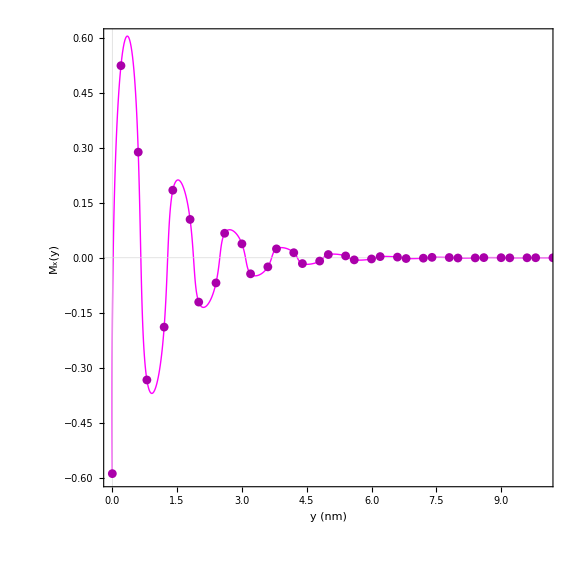

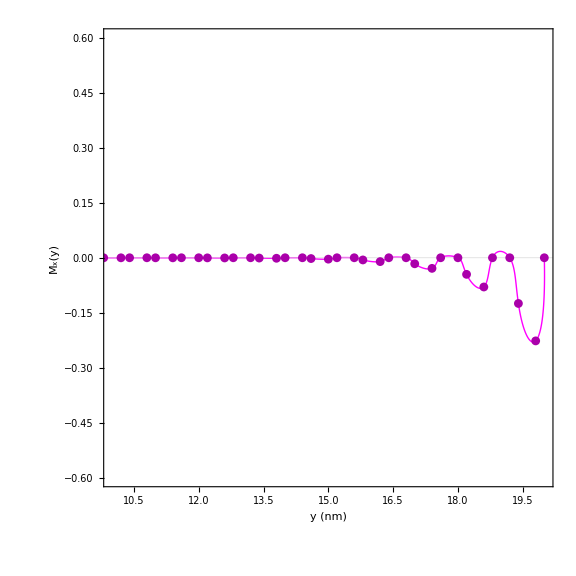

```mathematica
(*Show[Table[ListPlot[xmag[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[RGBColor["#789953"],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","M_x(y)"},PlotTheme->"Scientific"],{j,1,Length[xmag]}],ImageSize->Large,PlotRange->All]

Show[Table[ListPlot[ymag[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[RGBColor["#789953"],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","M_y(y)"},PlotTheme->"Scientific"],{j,1,Length[xmag]}],ImageSize->Large,PlotRange->All]
*)
xAvg={};
Do[
Do[
AppendTo[xAvg,Mean[Split[xmag[[l]],#1[[1]]==#2[[1]]&][[j]]]]
,{j,1,Length[Split[xmag[[l]],#1[[1]]==#2[[1]]&]]}]
,{l,1,Length[xmag]}]
xmagAvg=Table[{xAvg[[1;;2Num]][[j]][[1]],xAvg[[1;;2Num]][[j]][[2]]+xAvg[[2Num+1;;4Num]][[j]][[2]]},{j,1,Length[xAvg[[1;;2Num]]]}];

yAvg={};
Do[
Do[
AppendTo[yAvg,Mean[Split[ymag[[l]],#1[[1]]==#2[[1]]&][[j]]]]
,{j,1,Length[Split[ymag[[l]],#1[[1]]==#2[[1]]&]]}]
,{l,1,Length[ymag]}]
ymagAvg=Table[{yAvg[[1;;2Num]][[j]][[1]],yAvg[[1;;2Num]][[j]][[2]]+yAvg[[2Num+1;;4Num]][[j]][[2]]},{j,1,Length[yAvg[[1;;2Num]]]}];

magx3=ListPlot[xmagAvg,PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Magenta],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","M_x(y)"},PlotTheme->"Scientific",ImageSize->Large];
max3joined = ListPlot[xmagAvg,PlotRange->All,Joined->True,InterpolationOrder->10,PlotStyle->Directive[Magenta,Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","M_x(y)"},PlotTheme->"Scientific",ImageSize->Large];

magy3=ListPlot[ymagAvg,PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Magenta],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","M_x(y)"},PlotTheme->"Scientific",ImageSize->Large];
magy3joined=ListPlot[ymagAvg,PlotRange->All,Joined->True,InterpolationOrder->10,PlotStyle->Directive[Magenta,Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","M_x(y)"},PlotTheme->"Scientific",ImageSize->Large];

TestEmptyListy={};
Do[
AppendTo[TestEmptyListy,Chop[ymagAvg][[j]][[2]]]
,{j,1,Length[ymagAvg]}]

vy=ListInterpolation[TestEmptyListy,{0,(3/2(Num)-1)*(0.4)}];
magy31=Plot[vy[x],{x,0,(3/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","m_y(y)"},PlotStyle->Directive[Magenta,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large];

TestEmptyListx={};
Do[
AppendTo[TestEmptyListx,Chop[xmagAvg][[j]][[2]]]
,{j,1,Length[xmagAvg]}]

vx=ListInterpolation[TestEmptyListx,{0,(3/2(Num)-1)*(0.4)}];
magx31=Plot[vx[x],{x,0,(3/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","m_x(y)"},PlotStyle->Directive[Magenta,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large];

Show[max3joined,magx3,GridLinesStyle->Thick,FrameStyle->Thick,AspectRatio->1,PlotRange->{{0,10},{-0.6,0.6}}]
Show[magy3joined,magy3,(*magy11,magy1,magy21,magy2,*)GridLinesStyle->Thick,FrameStyle->Thick,AspectRatio->1,PlotRange->{{10,20},{-0.6,0.6}}]

(*Plot[vy[x]+vx[x],{x,0,((√3)/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","m_x(x)"},PlotStyle->Directive[Lighter[RGBColor["#789953"]],Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]*)
```

## Coupling

### Single Edge

```mathematica
NSteps=50;
Num=40;

l=(3/2*Num-1)*a;
d=17.5;
k=MeanMom[3.27,0.01][[1]][[2]];
numba=MeanMom[3.27,0.01][[1]][[1]];

F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)


Quiet[
Do[
y=l/a-30+j*N[50/NSteps];
x=0;
(*FIXED ENERGY*)
gy=F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,k,Num,numba,x,y,d,-√3*300,√3*300];
(*gy=F*MZNRCouplingContinuousTest[J,J2,DM,s,κ,h,ϕ,k,Num,numba,x,y,d,-1000,1000];*)
gm[y]={0.4*y,gy};
,{j,0,NSteps}];

];
```

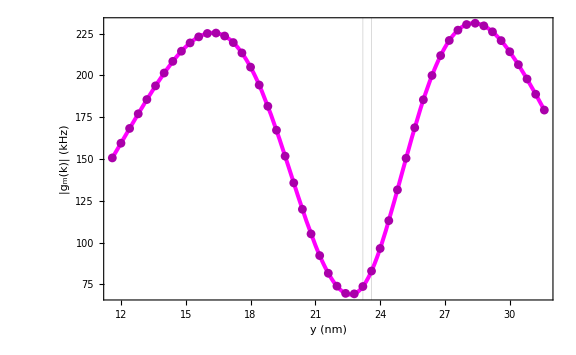

```mathematica
(*cplot=ListPlot[Table[gm[y],{y,l/a-20,l/a+10,N[30/NSteps]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],
FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Blue,Thickness[.005]],PlotRange->All,PlotTheme->"Scientific",Joined-> True];

Show[cplot,PlotRange->All,ImageSize->Large]*)

Test={};
Do[
AppendTo[Test,Table[gm[y],{y,l/a-30,l/a+20,N[50/NSteps]}][[j]][[2]]]
,{j,1,Length[Table[gm[y],{y,l/a-30,l/a+20,N[50/NSteps]}]]}]
v=ListInterpolation[Test,{0.4*(l/a-30),0.4*(l/a+20)}];
c71=Plot[v[x],{x,0.4*(l/a-30),0.4*(l/a+20)},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Magenta,Thickness[.005],Opacity[1]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{{(l/a-1)*0.4,23.6},{}}];
c7=ListPlot[Table[gm[y],{y,l/a-30,l/a+20,N[50/NSteps]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],
FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Darker[Magenta],Thickness[.005]],PlotRange->All,PlotTheme->"Scientific",Joined-> False];

Show[c71,c7]
```

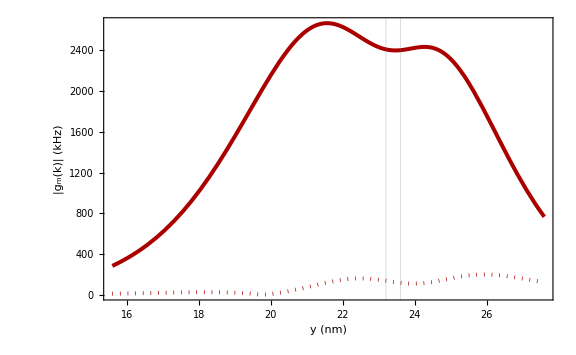

```mathematica
Show[p10,p11]
```

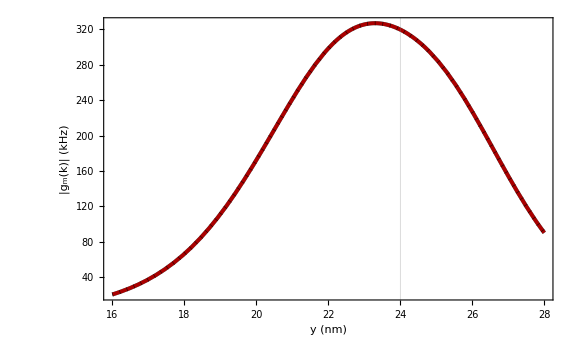

```mathematica
Show[p1,p2,p3]
```

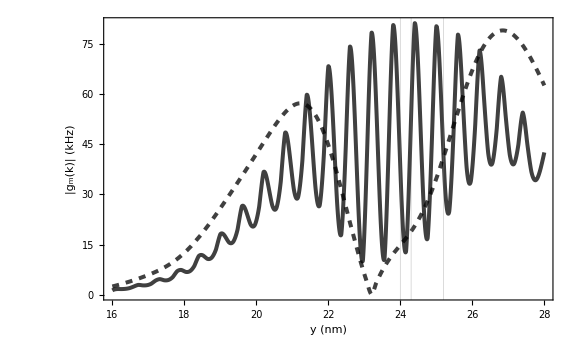

```mathematica
Show[p10,p12]
```

### Full Strip

```mathematica
WaveAlgo[J,J2,DM,s,κ,0,h,ϕ,Num,100,upperbound,lowerbound]

NSteps=34;
Num=34;
ω=3.1;
error=0.01;

l=(3/2*Num-1)*a;
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

CouplingList={};

AbsoluteTiming[
Do[
numba=MeanMom[ω,error][[j]][[1]];
mom=MeanMom[ω,error][[j]][[2]];
Do[
y=-10+l*N[(2Num)/NSteps];
x=0;
(*x=1/(√3)(l*N[80/NSteps]-10);*)
gy=F*MZNRCouplingDiscrete[J,J2,DM,s,0,0,h,ϕ,mom,Num,numba,x,y,d,-√3 500,√3 500];
gm[y]={0.4*y,gy};
,{l,0,NSteps}];

AppendTo[CouplingList,Table[gm[y],{y,-10,l/a+10,N[(2Num)/NSteps]}]];

,{j,1,Length[MeanMom[ω,error]]}];

]

Export["MZNR-SCQ_couple_omega=3.2.mx",CouplingList];
```

{871.779,Null}

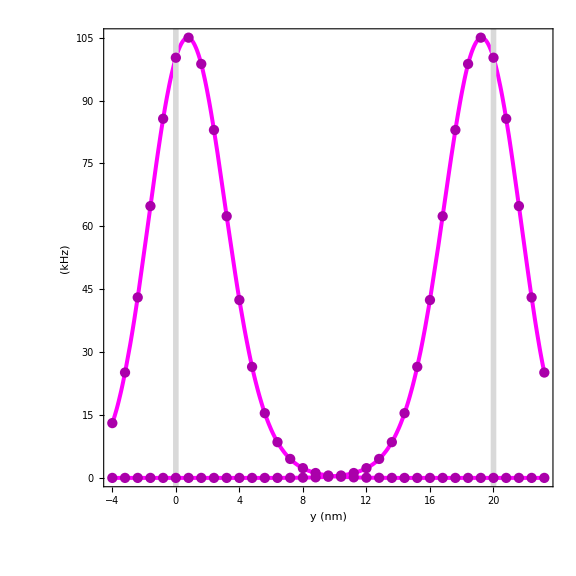

```mathematica
TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,CouplingList[[i]][[j]][[2]]]
,{j,1,Length[CouplingList[[i]]]-1}];
,{i,1,Length[CouplingList]}];

Do[

v=ListInterpolation[TestEmptyList[[(Length[CouplingList[[j]]]-1)*(j-1)+1;;(Length[CouplingList[[j]]]-1)*j]],{-4,23.2}];
plot[j]=Plot[v[x],{x,-4,23.2},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","(kHz)"},PlotStyle->Directive[Magenta,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[CouplingList]}];

c11=Show[Table[plot[j],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All,GridLines->{{0,(3/2*Num-1)*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]];

c1=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Magenta],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)",""},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All];

Show[c11,c1,(*c21,c2,c31,c3,*)(*c41,c4,c51,c5,c61,c6*)FrameStyle->Thick,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->36}],(*PlotRange->{All}*)AspectRatio->1]
```

Part::partw: Part 2 of gm[60.] does not exist.

ListPlot::ioproc: {{-4.,13.0783},{-3.2,25.1391},{-2.4,43.0539},{-1.6,64.8404},{-0.8,85.6691},{0.,100.227},{0.8,105.011},{1.6,98.7374},{2.4,82.9859},{3.2,62.413},«26»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

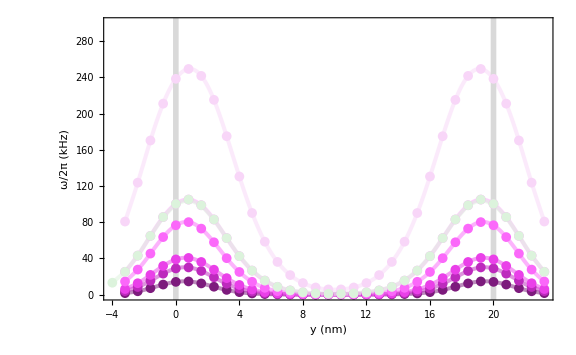

```mathematica
MZNRcup290=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=2.9.mx"];
MZNRcup295=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=2.95.mx"];
MZNRcup300=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=3.mx"];
MZNRcup305=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=3.05.mx"];
MZNRcup310=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=3.1.mx"];
MZNRcup315=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=3.15.mx"];
MZNRcup320=Import["C:\\Users\\jeffc\\Documents\\MZNR-SCQ_couple_omega=3.2.mx"];

MZNRcup2=Reverse[{MZNRcup290,MZNRcup295,MZNRcup300,MZNRcup305,MZNRcup310,MZNRcup315,MZNRcup320}];
(*Go through above list, create a new list that keeps the first element (position) the same and takes the mean of the left and right edge*)
MZNRcup3=Table[Table[{MZNRcup2[[j]][[1]][[i]][[1]],MZNRcup2[[j]][[1]][[i]][[2]]+MZNRcup2[[j]][[2]][[i]][[2]]},{i,2,Length[MZNRcup2[[j]][[1]]]-1}],{j,1,Length[MZNRcup2]}];

MZNRcup290Scaled=Table[Table[{MZNRcup290[[i]][[j]][[1]],3*MZNRcup290[[i]][[j]][[2]]},{j,2,Length[MZNRcup290[[i]]]-1}],{i,1,Length[MZNRcup290]}];
MZNRcup295Scaled=Table[Table[{MZNRcup295[[i]][[j]][[1]],3*MZNRcup295[[i]][[j]][[2]]},{j,2,Length[MZNRcup295[[i]]]-1}],{i,1,Length[MZNRcup295]}];
MZNRcup300Scaled=Table[Table[{MZNRcup300[[i]][[j]][[1]],2*MZNRcup300[[i]][[j]][[2]]},{j,2,Length[MZNRcup300[[i]]]-1}],{i,1,Length[MZNRcup300]}];
MZNRcup305Scaled=Table[Table[{MZNRcup305[[i]][[j]][[1]],2*MZNRcup305[[i]][[j]][[2]]},{j,2,Length[MZNRcup305[[i]]]-1}],{i,1,Length[MZNRcup305]}];
MZNRcup310Scaled=Table[Table[{MZNRcup310[[i]][[j]][[1]],MZNRcup310[[i]][[j]][[2]]},{j,2,Length[MZNRcup310[[i]]]-1}],{i,1,Length[MZNRcup310]}];
MZNRcup315Scaled=Table[Table[{MZNRcup315[[i]][[j]][[1]],MZNRcup315[[i]][[j]][[2]]},{j,2,Length[MZNRcup315[[i]]]-1}],{i,1,Length[MZNRcup315]}];

MZNRcup2Scaled={MZNRcup290Scaled,MZNRcup295Scaled,MZNRcup300Scaled,MZNRcup305Scaled,MZNRcup310Scaled,MZNRcup315Scaled,MZNRcup320};
MZNRcup3Scaled=Table[Table[{MZNRcup2Scaled[[j]][[1]][[i]][[1]],MZNRcup2Scaled[[j]][[1]][[i]][[2]]+MZNRcup2Scaled[[j]][[2]][[i]][[2]]},{i,1,Length[MZNRcup2Scaled[[j]][[1]]]}],{j,1,Length[MZNRcup2Scaled]}];


poo2=Show[Table[ListPlot[MZNRcup3Scaled[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large,PlotMarkers->{Automatic,Medium}],{j,1,Length[MZNRcup3Scaled]}],PlotRange->All];
poo2smooth=Show[Table[ListPlot[MZNRcup3Scaled[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[MZNRcup3Scaled]}],PlotRange->All];
Show[poo2smooth,poo2,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotRange->{All,{0,300}}]
```

```mathematica
(*ListPlot[MZNRcup2[[7]]]*)
MeanMom[3.15,1/100]
```

{{60,0.471588,3.15504+0. ⅈ},{60,-0.471588,3.15504+0. ⅈ}}

```mathematica
MZNRcupNames={"MZNR-SCQ_Couple_omega=2.9_combined_indv_Scaled.svg","MZNR-SCQ_Couple_omega=2.95_combined_indv_Scaled.svg","MZNR-SCQ_Couple_omega=3_combined_indv_Scaled.svg","MZNR-SCQ_Couple_omega=3.05_combined_indv_Scaled.svg","MZNR-SCQ_Couple_omega=3.1_combined_indv_Scaled.svg","MZNR-SCQ_Couple_omega=3.15_combined_indv_Scaled.svg"};

ColorzzzL={Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]]};
ColorzzzR={Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Red]]};

Do[
Test1=ListPlot[MZNRcup3Scaled[[k]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(9+k)/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smooth=ListPlot[MZNRcup3Scaled[[k]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(9+k)/15],Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1L=ListPlot[MZNRcup2Scaled[[k]][[1]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorzzzL[[k]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothL=ListPlot[MZNRcup2Scaled[[k]][[1]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorzzzL[[k]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1R=ListPlot[MZNRcup2Scaled[[k]][[2]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorzzzR[[k]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothR=ListPlot[MZNRcup2Scaled[[k]][[2]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorzzzR[[k]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

plottest=Show[Test1smoothL,Test1L,Test1smoothR,Test1R,Test1smooth,Test1,ImageSize->Large,FrameStyle->Thickness[0.01],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.01]],PlotMarkers->Automatic,PlotRange->{All,{0,300}}];

Export[MZNRcupNames[[k]],plottest]
,{k,1,Length[MZNRcup3Scaled]}];
```

### Edge Couple vs. d

```mathematica
Num=34;

ω=3.15;

mom=MeanMom[ω,0.01][[2]][[2]];
numba=MeanMom[ω,0.01][[2]][[1]];
l=(3/2*Num-1)*a;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)
Gmax=Table[{r,F*MZNRCouplingDiscreteTest[J,J2,DM,s,0,h,ϕ,mom,Num,numba,0,0,r,-√3 500,√3 500]},{r,1,25,0.5}];

Export["MZNR-SCQ_edge_vs_d_omega=3.1.mx",Gmax]
```

$Aborted

MZNR-SCQ_edge_vs_d_omega=3.1.mx

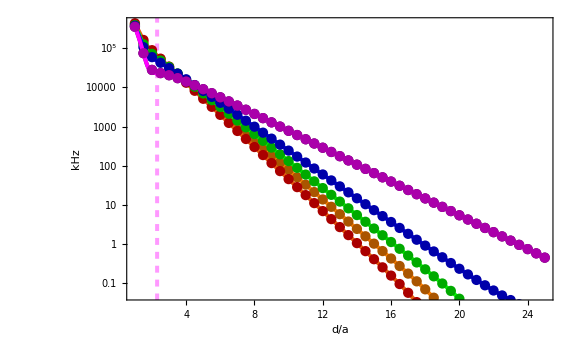

```mathematica
Gmax=Import["MZNR-SCQ_edge_vs_d_omega=2.9.mx"];

p1=ListLogPlot[Gmax,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a",""},PlotStyle->Directive[Darker[Red],Thickness[.009]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,FrameTicks->Automatic];

TestEmptyList={};
Do[
AppendTo[TestEmptyList,Gmax[[j]][[2]]]
,{j,1,Length[Gmax]}]

v=ListInterpolation[TestEmptyList,{1,25}];
p11=LogPlot[v[x],{x,1,25},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","kHz"},PlotStyle->Directive[Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large];

(*Show[p11,p1,p21,p2,p31,p3,p41,p4,p61,p6,p51,p511,p5,p0,p01,PlotRange->All]*)
Show[p21,p2,p11,p1,p31,p3,p41,p4,p51,p5,p61,p6,PlotRange->{All,{-3,13}},GridLines->{{{2.3,Directive[Magenta,Dashed,Thickness[0.005]]}},{}}]
```

```mathematica
mznrE290=Import["MZNR-SCQ_edge_vs_d_omega=2.9.mx"];
mznrE295=Import["MZNR-SCQ_edge_vs_d_omega=2.95.mx"];
mznrE300=Import["MZNR-SCQ_edge_vs_d_omega=3.mx"];
mznrE305=Import["MZNR-SCQ_edge_vs_d_omega=3.05.mx"];
mznrE310=Import["MZNR-SCQ_edge_vs_d_omega=3.1.mx"];
mznrE315=Import["MZNR-SCQ_edge_vs_d_omega=3.15.mx"];

MZNRedge={mznrE290,mznrE295,mznrE300,mznrE305,mznrE310,mznrE315};
```

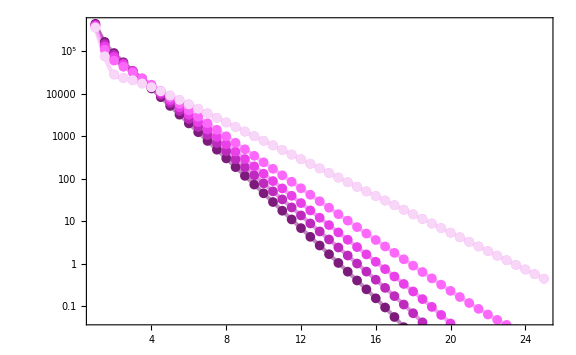

```mathematica
edgeplot=Show[Table[ListLogPlot[MZNRedge[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large,PlotMarkers->{Automatic,Medium}],{j,1,Length[MZNRedge]}],PlotRange->All];
edgeplotsmooth=Show[Table[ListLogPlot[MZNRedge[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Opacity[0.5],Thickness[0.005]],Ticks->{{0,5,10,15,20,25},{0,Log[10^2],Log[10^4]}},
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[MZNRedge]}],PlotRange->All];
Show[edgeplotsmooth,edgeplot,FrameStyle->Thickness[0.01],GridLines->{{5,10,15,20},{0,Log[10^2],Log[10^4]}},GridLinesStyle->Thickness[0.002],PlotRange->{All,{-3,13}}]
```

### Stray Field Vs. d

```mathematica
Num=34;
ω=2.9;

mom=MeanMom[ω,0.01][[2]][[2]];
numba=MeanMom[ω,0.01][[2]][[1]];
hy=Table[{r,MZNRStrayField[J,J2,DM,s,0,h,ϕ,mom,Num,numba,0,0,r,-√3*500,√3*500][[2]]},{r,2,25,0.5}];
Export["MZNR_hy_v_d_omega=2.9.mx",hy];
```

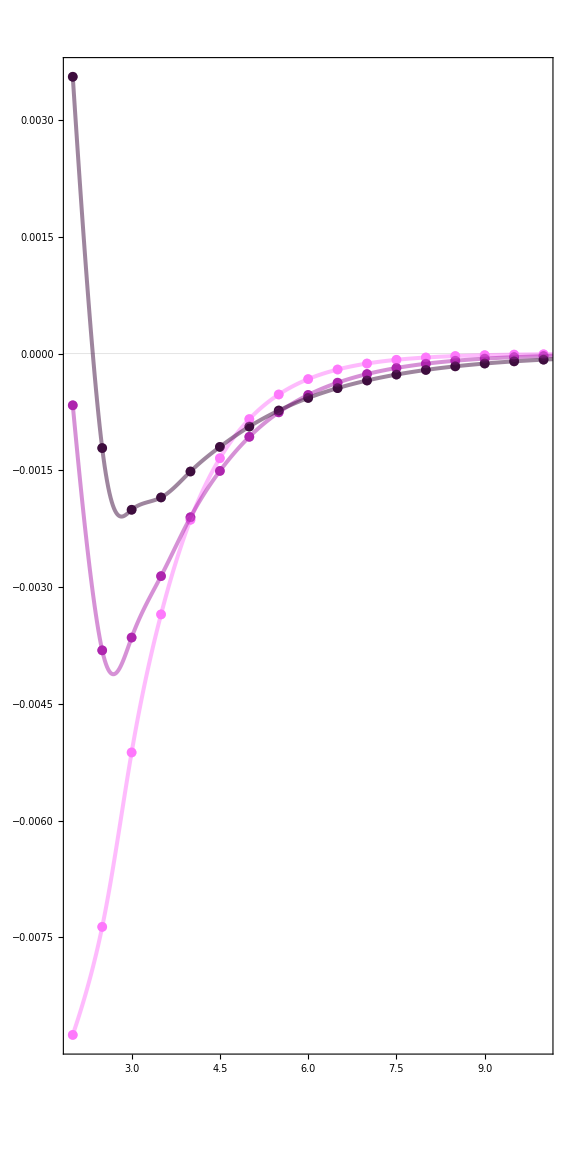

```mathematica
hx290=Import["MZNR_hx_v_d_omega=2.9.mx"];
hx305=Import["MZNR_hx_v_d_omega=3.05.mx"];
hx315=Import["MZNR_hx_v_d_omega=3.15.mx"];

hx={hx290,hx305,hx315};

Colors={ColorData["GreenPinkTones",10/15],ColorData["GreenPinkTones",13/15],ColorData["GreenPinkTones",15/15]};

Bx=Table[ListPlot[hx[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Colors[[j]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[hx]}];

Bxsmooth=Table[ListPlot[hx[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Colors[[j]],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[hx]}];;

(*hx3=ListPlot[hy,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","(a.u.)"},PlotStyle->Directive[Darker[Magenta],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,GridLines->{{},{0}}];*)


Show[Bx,Bxsmooth,GridLinesStyle->Directive[Thick],FrameStyle->Directive[Thickness[0.02]],AspectRatio->2,GridLines->{{0},{0}},PlotRange->{{2,10},All}]
```

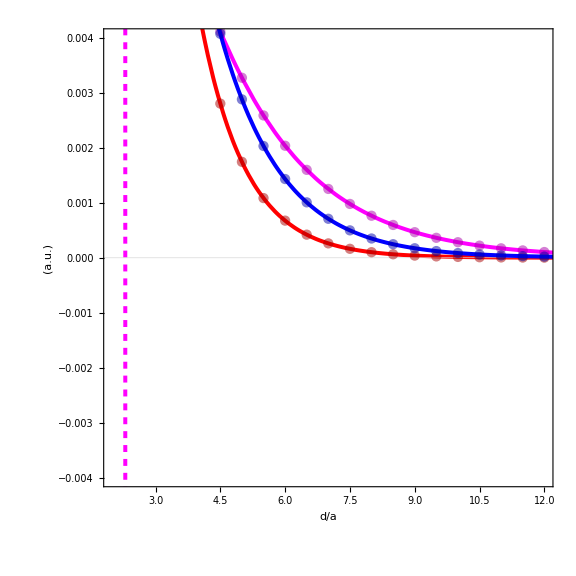

```mathematica
hy=Import["MZNR_hy_v_d_omega=2.9.mx"];

hy1=ListPlot[hy,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","(a.u.)"},PlotStyle->Directive[Darker[Red],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All(*{{5,50},{-100*10^-6,100*10^-6}}*),ImageSize->Large,GridLines->{{},{0}}];

TestEmptyList={};
Do[
AppendTo[TestEmptyList,hy[[j]][[2]]]
,{j,1,Length[hy]}]

v=ListInterpolation[TestEmptyList,{2,25}];
hy11=Plot[v[x],{x,2,25},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"d/a","(a.u.)"},PlotStyle->Directive[Red,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large];

Show[hy11,hy1,hy31,hy3,hy21,hy2,GridLinesStyle->Directive[Thick],FrameStyle->Directive[Thick],AspectRatio->1,GridLines->{{{2.3,Directive[Magenta,Dashed,Thickness[0.005]]}},{0}},PlotRange->{{2,12},{-0.004,0.004}}]
```

### Anisotropy

```mathematica
Δκ=0.3;
κ=0.3;
WaveAlgo[J,J2,DM,s,κ,Δκ,h,ϕ,Num,Naux,upperbound,lowerbound];

NSteps=34;
Num=34;
ω=3.1+κ/(2Pi ℏ);
error=1/(2Naux);

l=(3/2*Num-1)*a;
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

CouplingList={};

AbsoluteTiming[
Do[
numba=MeanMom[ω,error][[j]][[1]];
mom=MeanMom[ω,error][[j]][[2]];
Do[
y=-10+k*N[(2Num)/NSteps];
x=0;
(*x=1/(√3)(l*N[80/NSteps]-10);*)
gy=F*MZNRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,mom,Num,numba,x,y,d,-√3 500,√3 500];
gm[y]={0.4*y,gy};
,{k,0,NSteps+1}];

AppendTo[CouplingList,Table[gm[y],{y,-10,l/a+10,N[(2Num)/NSteps]}]];

,{j,1,Length[MeanMom[ω,error]]}];
]

Export["MZNR-SCQ_couple_omega=3.1_kap=0.3_delkap=0.3.mx",CouplingList];
```

{872.649,Null}

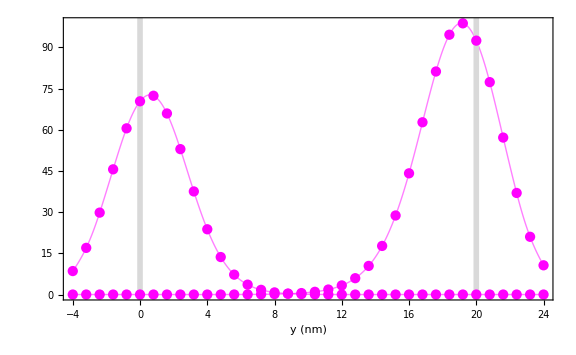

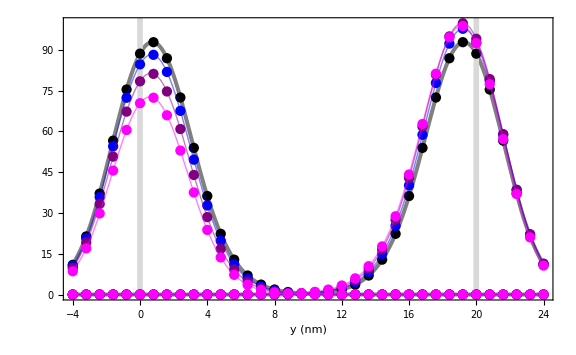

```mathematica
p4=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Magenta,Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)",""},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All];
p4joined=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->True,InterpolationOrder->10,PlotStyle->Directive[Magenta,Thick,Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)",""},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All];

(*TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,CouplingList[[i]][[j]][[2]]]
,{j,1,Length[CouplingList[[i]]]-1}];
,{i,1,Length[CouplingList]}];

Do[

v=ListInterpolation[TestEmptyList[[(Length[CouplingList[[j]]]-1)*(j-1)+1;;(Length[CouplingList[[j]]]-1)*j]],{-4,24}];
plot[j]=Plot[v[x],{x,-4,24},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","(kHz)"},PlotStyle->Directive[Gray,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[CouplingList]}];

p1smooth=Show[Table[plot[j],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All,GridLines->{{0,(3/2*Num-1)*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]];*)

Show[p4joined,p4,PlotRange->{{-4,24},All},GridLines->{{0,(3/2*Num-1)*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]]
Show[p1joined,p1,p2joined,p2,p3joined,p3,p4joined,p4,PlotRange->{{-4,24},All},GridLines->{{0,(3/2*Num-1)*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]]
```

```mathematica
Show[-Graphics-,FrameStyle->Thick,FrameLabel->{"y (nm)","|g_m(k)|/2π (kHz)"}]
```

-Graphics-

```mathematica
Zkap1=Import["MZNR-SCQ_couple_omega=3.1_kap=0.3_delkap=0.1.mx"];
Zkap2=Import["MZNR-SCQ_couple_omega=3.1_kap=0.3_delkap=0.2.mx"];
Zkap3=Import["MZNR-SCQ_couple_omega=3.1_kap=0.3_delkap=0.3.mx"];
Zkap={Zkap1,Zkap2,Zkap3};

MZNRKapCom=Table[Table[{Zkap[[j]][[1]][[i]][[1]],Zkap[[j]][[1]][[i]][[2]]+Zkap[[j]][[2]][[i]][[2]]},{i,1,Length[Zkap[[j]][[1]]]}],{j,1,Length[Zkap]}];
```

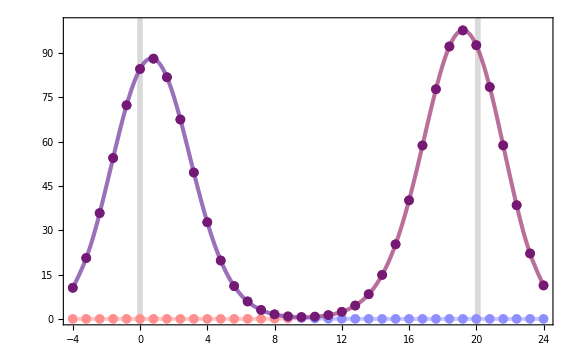

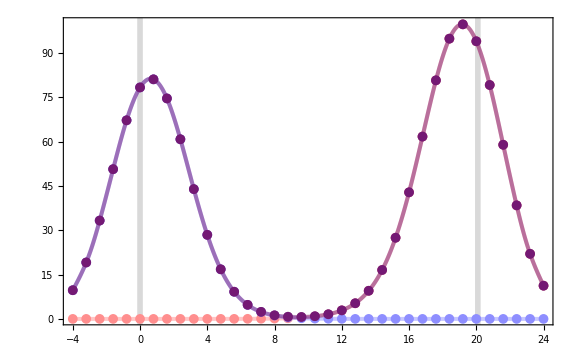

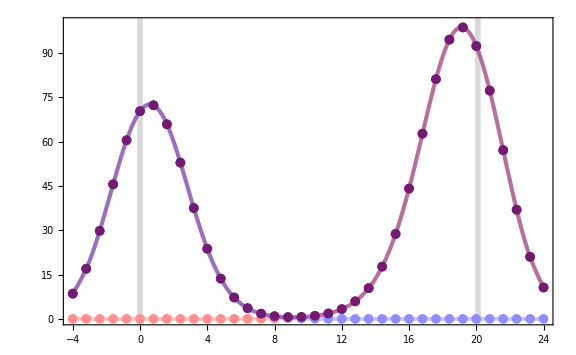

```mathematica
Colors={Blue,Red};

p0Com=Show[ListPlot[MZNRKapCom[[1]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->{All,{0,70}}];
p0smoothCom=Show[ListPlot[MZNRKapCom[[1]],Joined->True,InterpolationOrder->3,PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

p1Com=Show[ListPlot[MZNRKapCom[[2]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];
p1smoothCom=Show[ListPlot[MZNRKapCom[[2]],Joined->True,InterpolationOrder->3,PlotRange->All,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

p2Com=Show[ListPlot[MZNRKapCom[[3]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];
p2smoothCom=Show[ListPlot[MZNRKapCom[[3]],Joined->True,InterpolationOrder->3,PlotRange->All,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

plotcol={Directive[Lighter[Lighter[Red]],Thickness[0.005]],Directive[Lighter[Lighter[Blue]],Thickness[0.005]]};
plotcolopac={Directive[Lighter[Lighter[Red]],Thickness[0.005],Opacity[0.5]],Directive[Lighter[Lighter[Blue]],Thickness[0.005],Opacity[0.5]]};

p1=Show[Table[ListPlot[Zkap1[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[Zkap1]}],ImageSize->Large,PlotRange->All];
p1smooth=Show[Table[ListPlot[Zkap1[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[Zkap1]}],ImageSize->Large,PlotRange->All];

p2=Show[Table[ListPlot[Zkap2[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[Zkap2]}],ImageSize->Large,PlotRange->All];
p2smooth=Show[Table[ListPlot[Zkap2[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[Zkap2]}],ImageSize->Large,PlotRange->All];

p3=Show[Table[ListPlot[Zkap3[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[Zkap3]}],ImageSize->Large,PlotRange->All];
p3smooth=Show[Table[ListPlot[Zkap3[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[Zkap3]}],ImageSize->Large,PlotRange->All];


(*Show[p0,p0smooth,p0Com,p0smoothCom,PlotRange->{All,{0,70}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]*)
Show[p1,p1smooth,p0Com,p0smoothCom,PlotRange->{All,{0,100}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
Show[p2,p2smooth,p1Com,p1smoothCom,PlotRange->{All,{0,100}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
Show[p3,p3smooth,p2Com,p2smoothCom,PlotRange->{All,{0,100}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
```

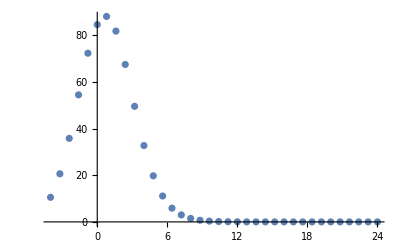

```mathematica
ListPlot[Zkap[[1]][[2]]]
```

### How does coupling on the right edge depend on kappa?

```mathematica
(*The following function is going to be a little redundant, since it isn't much different than WaveAlgo, but it is my hope
that it will be more efficient.*)

Naux=1000;
Num=34;
κ=0.3;
ω=3.1+κ/(2Pi ℏ);
error=1/Naux;

EdgeCoupleList={};

Module[{ka,EdgeCouple,l,Δκ},
Do[

Δκ=0+0.03*m;

WaveAlgo[J,J2,DM,s,κ,Δκ,h,ϕ,Num,Naux,upperbound,lowerbound];

l=50;

ka=MeanMom[ω,error][[1]][[2]];

EdgeCouple = F*MZNRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,ka,Num,numba,0,l,d,-√3 500,√3 500];

AppendTo[EdgeCoupleList,{Δκ,EdgeCouple}];

,{m,0,10}];
];

(*The following are essentially the same as FindIndices and MeanMom defined above but with minor alterations to try to increase efficiency.*)



(*FindIndices2[Naux_,Num_,lb_,ub_,J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_]:=
Module[{EmptyList,omegas,H,A,sortorder},

EmptyList={};

Do[
ξ=-Pi/(√3)+j* N[(2 Pi/(√3))/Naux];

H=MZNRMatrix2N[J,J2,s,DM,h,κ,Δκ,ξ,ϕ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

omegas=Table[Table[f[ξ][[j]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[100]],{j,1,Length[Table[f[ξ],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[100]]]}];
(*Note that omegas is the table of frequencies for some positive momentum. This will suffice for finding the band indices. *)


Do[
If[lb<omegas[[j]]<ub,AppendTo[EmptyList,j]]
,{j,1,Length[omegas]}];

EmptyList
]

MeanMom2[ω_,err_,Naux_,Num_,lb_,ub_,J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_]:=
Module[{BandIndices,EmptyList,Mom,MomList,EmptyList2},
BandIndices=FindIndices2[Naux,Num,lb,ub,J,J2,DM,s,κ,Δκ,h,ϕ];

EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&];

MomList=Split[Mom,Abs[#1[[2]]-#2[[2]]]<err&&#1[[1]]==#2[[1]]&];
EmptyList2={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList2,Mean[MomList[[i]]]]];

EmptyList2
]

KappaMom={};

Module[{k,ka,EdgeCouple,mean,numba,κ,Δκ,KappaLine},

κ=0.3;

Do[


Δκ=0+0.03*m;

mean=MeanMom2[3.1+κ/(2Pi ℏ),1/(2Naux),Naux,Num,2.3,3.1,J,J2,DM,s,κ,Δκ,h,ϕ];
k=mean[[1]][[2]];
numba=mean[[1]][[1]];

AppendTo[KappaMom,{Δκ,Around[k,1/(2Naux)]}];

,{m,0,10}];

];

EdgeCoupleList={};

Module[{ka,EdgeCouple,l,Δκ},
Do[

Δκ=0+0.03*m;

l=(3/2*Num-1);

ka=KappaMom[[m+1]][[2]][[1]];

EdgeCouple = F*MZNRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,mom,Num,numba,l,0,d,-√3500,√3 500];

AppendTo[EdgeCoupleList,{Δκ,EdgeCouple}];

,{m,0,10}];
];*)
```

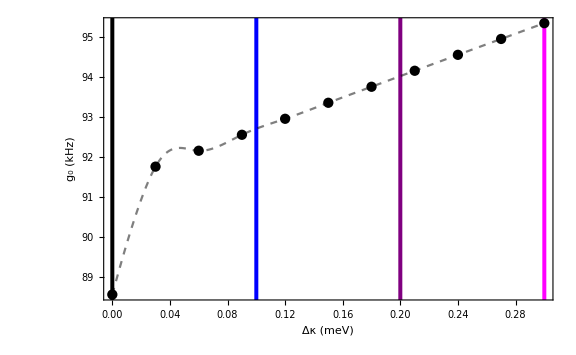

```mathematica
thisplot2=ListPlot[EdgeCoupleList,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","g_0 (kHz)"},PlotStyle->Directive[Black],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
thisplotj2=ListPlot[EdgeCoupleList,Joined->True,InterpolationOrder->3,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Black,Dashed,Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1];
thisotherplot=ListPlot[KappaMom,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ka"},PlotStyle->Directive[Red],PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1];
thisotherplotj=ListPlot[KappaMom,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Red,Opacity[0.5]],PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1];

Clear[x]
KappaLine=LinearModelFit[KappaMom,x,x];
nlm2=NonlinearModelFit[KappaMom,α+β x+γ x^2,{α,β,γ},x];
KappaLinePlot=Plot[KappaLine[x],{x,0,0.3},PlotStyle->Directive[Black],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{""},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
KappaLinePlotD=Plot[KappaLine'[x],{x,0,0.3},PlotStyle->Directive[Lighter[Black]]];
nlm2Plot=Plot[nlm2[x],{x,0,0.3},PlotStyle->Directive[Blue]];
nlm2PlotD=Plot[nlm2'[x],{x,0,0.3},PlotStyle->Directive[Lighter[Blue]]];
nlm2PlotD2=Plot[nlm2''[x],{x,0,0.3},PlotStyle->Directive[Lighter[Cyan]]];

Show[(*thisplot,thisplotj*)thisplot2,thisplotj2,GridLines->{{{0,Black},{0.1,Blue},{0.2,Purple},{0.3,Magenta}},{}},PlotRange->All,GridLinesStyle->Directive[Thickness[0.005]]]
(*Show[thisotherplot,thisotherplotj,KappaLinePlot,nlm2Plot(*,GridLines->{{0.075,0.105,0.165,0.195,0.225,0.24,0.27,0.285},{}}*),AspectRatio->1/GoldenRatio]
Show[KappaLinePlot,KappaLinePlotD,nlm2Plot,nlm2PlotD]*)
```

```mathematica
F*MZNRCouplingDiscrete[J,J2,DM,s,κ,0.1,h,ϕ,ka,Num,numba,0,l,d,-√3 500,√3 500]
```

$Aborted

```mathematica
MeanMom[ω,error]
```

{{35,0.594926,3.17145},{35,-0.616692,3.17163}}

```mathematica
numba
```

35

{{35,0.594926,3.17145},{35,-0.616692,3.17163}}

```mathematica
F*MZNRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,0.5949261914688238,Num,35,0,50,d,-√3 500,√3 500]
```

92.4238

## Maximum Coupling as a Function of Vertical Distance

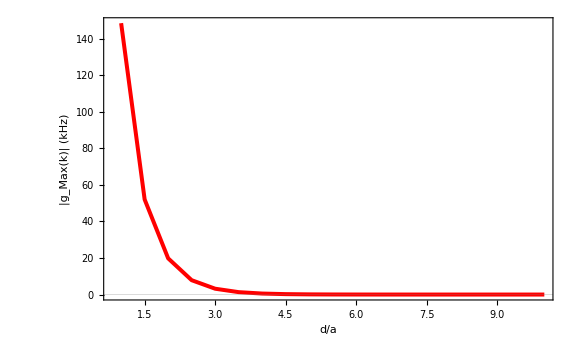

```mathematica
Num=50;
l=3/2*2*Num*a;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3; (*KHz*)
ListPlot[Table[{r,F*MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.6,Num,Num,0,1.6,r]},{r,1,10,0.5}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"d/a","|g_Max(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotTheme->"Scientific",Joined-> True,PlotRange->All,ImageSize->Large]
```

## Maximum Coupling as a function of Energy

```mathematica
Naux=200;
Num=50;


Do[
ξ=j* N[(Pi/(√3))/Naux];

H=MZNRMatrix2N[J,J2,s,DM,h,κ,ξ,ϕ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]
```

```mathematica
RightLowerBand=Select[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],#[[1]]>0&];
LeftUpperBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],#[[1]]<0&];
PositiveBand=Select[Join[RightLowerBand,LeftUpperBand],2.2<#[[2]]<3.2&];
```

```mathematica
d=1;
g={};
Do[
Quiet[
MaxCoupling=MZNRCoupling[J,J2,DM,s,κ,h,ϕ,PositiveBand[[i]][[1]],Num,Num,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,PositiveBand[[i]][[1]],Num,Num+1,0,150,d];
AppendTo[g,{PositiveBand[[i]][[2]],MaxCoupling}]
]
,{i,1,Length[PositiveBand]}]
```

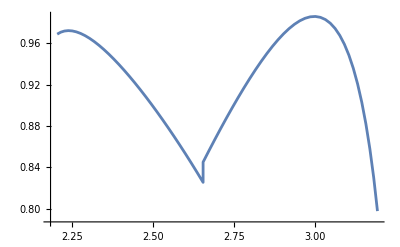

```mathematica
ListPlot[g,Joined->True]
```

```mathematica
g
```

{{2.20429,0.150845},{2.21519,0.14904},{2.22656,0.147127},{2.23839,0.145117},{2.25066,0.143023},{2.26337,0.140855},{2.27648,0.138623},{2.29,0.136337},{2.30389,0.134005},{2.31815,0.131633},{2.33275,0.12923},{2.34768,0.126801},{2.36293,0.124352},{2.37847,0.121889},{2.39429,0.119415},{2.41037,0.116936},{2.4267,0.114455},{2.44326,0.111976},{2.46003,0.109503},{2.47699,0.107037},{2.49414,0.104581},{2.51144,0.102139},{2.52889,0.0997119},{2.54647,0.0973015},{2.56417,0.0949097},{2.58196,0.0925379},{2.59984,0.0901875},{2.61778,0.0878595},{2.63577,0.0855549},{2.65379,0.0832745},{2.65379,0.0911945},{2.67184,0.0939695},{2.68989,0.0967839},{2.70793,0.0996347},{2.72594,0.102518},{2.74392,0.105431},{2.76184,0.108368},{2.7797,0.111323},{2.79747,0.114292},{2.81515,0.117268},{2.83272,0.120243},{2.85018,0.12321},{2.86749,0.126158},{2.88466,0.129079},{2.90167,0.131961},{2.91851,0.134791},{2.93516,0.137557},{2.95162,0.140242},{2.96787,0.142831},{2.98391,0.145304},{2.99971,0.147642},{3.01527,0.149823},{3.03058,0.15182},{3.04563,0.153607},{3.06041,0.155153},{3.0749,0.156423},{3.0891,0.157379},{3.10299,0.157977},{3.11658,0.15817},{3.12984,0.157899},{3.14277,0.157101},{3.15536,0.155701},{3.16761,0.153608},{3.17949,0.150714},{3.19101,0.146886}}

```mathematica
EmptyList={};
Do[
AppendTo[EmptyList,{i,i^2}]
,{i,0,5}]
```

```mathematica
EmptyList
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25}}

```mathematica
Table[g[PositiveBand[[i]][[2]]],{i,1,Length[PositiveBand]}]
```

{g[2.20429],g[2.21519],g[2.22656],g[2.23839],g[2.25066],g[2.26337],g[2.27648],g[2.29],g[2.30389],g[2.31815],g[2.33275],g[2.34768],g[2.36293],g[2.37847],g[2.39429],g[2.41037],g[2.4267],g[2.44326],g[2.46003],g[2.47699],g[2.49414],g[2.51144],g[2.52889],g[2.54647],g[2.56417],g[2.58196],g[2.59984],g[2.61778],g[2.63577],g[2.65379],g[2.65379],g[2.67184],g[2.68989],g[2.70793],g[2.72594],g[2.74392],g[2.76184],g[2.7797],g[2.79747],g[2.81515],g[2.83272],g[2.85018],g[2.86749],g[2.88466],g[2.90167],g[2.91851],g[2.93516],g[2.95162],g[2.96787],g[2.98391],g[2.99971],g[3.01527],g[3.03058],g[3.04563],g[3.06041],g[3.0749],g[3.0891],g[3.10299],g[3.11658],g[3.12984],g[3.14277],g[3.15536],g[3.16761],g[3.17949],g[3.19101]}

```mathematica
Length[PositiveBand]
```

65

```mathematica
d=1;
Ek1={{2.4,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.6,Num,Num,0,1.6,d])},{2.6,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.72,Num,Num,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.8,Num,Num,0,1.6,d])},{2.8,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.63,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.71,Num,Num+1,0,1.6,d])},{3,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.4,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.5,Num,Num+1,0,1.6,d])},
{3.2,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.13,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.26,Num,Num+1,0,1.6,d])}};
Ek2={{2.4,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.6,Num,Num,0,150,d])},{2.6,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.72,Num,Num,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.8,Num,Num,0,150,d])},{2.8,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.63,Num,Num+1,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.71,Num,Num+1,0,150,d])},{3,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.4,Num,Num+1,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.5,Num,Num+1,0,150,d])},
{3.2,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.13,Num,Num+1,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.26,Num,Num+1,0,150,d])}};
```

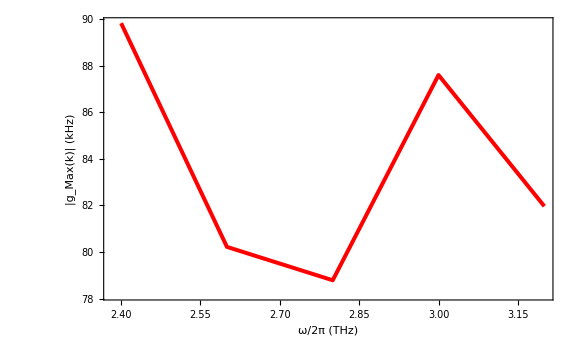

```mathematica
ListPlot[{Ek1},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"ω/2π (THz)","|g_Max(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotTheme->"Scientific",Joined-> True,PlotRange->All,ImageSize->Large]
```

```mathematica
Num=50;
l=3/2*2*Num*a;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3; (*KHz*)
d=3;
Ek1={{2.4,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.6,Num,Num,0,1.6,d])},{2.6,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.72,Num,Num,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.72,Num,Num,0,1.6,d])},
{2.65,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-Pi/(√3),Num,Num,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,Pi/(√3),Num,Num,0,1.6,d])},
{2.7,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.76,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.76,Num,Num+1,0,1.6,d])},
{2.7,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.76,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.76,Num,Num+1,0,1.6,d])},{2.8,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.63,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.63,Num,Num+1,0,1.6,d])},{3,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.4,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.4,Num,Num+1,0,1.6,d])},
{3.2,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.13,Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.13,Num,Num+1,0,1.6,d])}};
(*Ek2={{2.4,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.5,Num,Num,0,150,d])},{2.6,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.72,Num,Num,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.72,Num,Num,0,150,d])},{2.8,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.63,Num,Num+1,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.63,Num,Num+1,0,150,d])},{3,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.4,Num,Num+1,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.4,Num,Num+1,0,150,d])},
{3.2,F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.13,Num,Num+1,0,150,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.13,Num,Num+1,0,150,d])}};*)
```

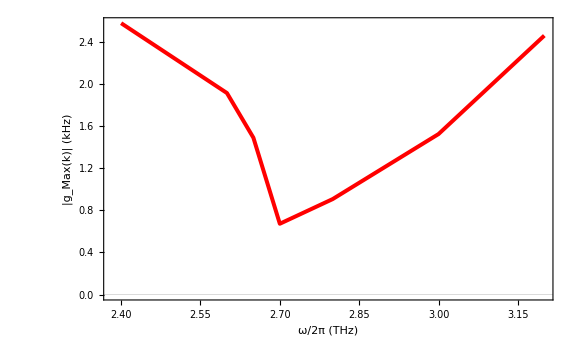

```mathematica
ListPlot[{Ek1},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"ω/2π (THz)","|g_Max(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotTheme->"Scientific",Joined-> True,PlotRange->All,ImageSize->Large]
```

```mathematica
F*(MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-Pi/(√3),Num,Num+1,0,1.6,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,Pi/(√3),Num,Num+1,0,1.6,d])
```

4.06085×10^-7

## MZNR w/ Impurities

### Dispersion

```mathematica
κ=0;
Naux=300;
Num=20;

Do[
ξ=-Pi/(√3)+j* N[((2Pi)/(√3))/Naux];

H=MZNRMatrix2NBImpure[J,J2,s,DM,h,κ,ξ,ϕ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]
```

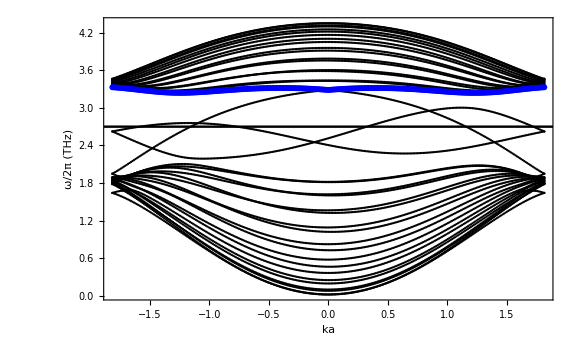

```mathematica
pimp=ListPlot[Table[f[ξ],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Black,Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"];
p1=ListPlot[Table[f[ξ][[23]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Blue,Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"];
Show[pimp,p1,PlotRange->All,ImageSize->Large,GridLines->{{},{2.7}},GridLinesStyle->Directive[Black,Thickness[.003]]]
```

### Wavefunction Algorithm

```mathematica
(*Calculate table of values*)
Naux=300;
Num=20;
upperbound=3.4;
lowerbound=2;

Do[
ξ=-Pi/(√3)+j* N[((2Pi)/(√3))/Naux];

H=MZNRMatrix2NBImpure[J,J2,s,DM,h,κ,ξ,ϕ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}];

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[Naux_,Num_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}]]}]
,{i,1,2Num}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
wavefunctions[ω_,err_]:=
Module[{wavefunction,U,f,k,band},
wavefunction={};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=ImpureUMatrixB[J,J2,DM,s,κ,h,ϕ,k,Num];
f=Table[{3/2 M *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMom[ω,err]]}];

wavefunction

];
```

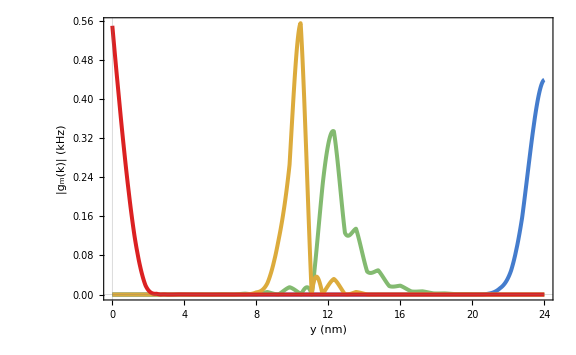

```mathematica
(*Plot that shit!*)
Wavefunctions=wavefunctions[2.3,0.01];

TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,Wavefunctions[[i]][[j]][[2]]]
,{j,1,Length[Wavefunctions[[i]]]}];
,{i,1,Length[Wavefunctions]}];


Do[
v=ListInterpolation[TestEmptyList[[40*(j-1)+1;;40j]],{0,24}];
plot[j]=Plot[Abs[v[x]],{x,0,24},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[ColorData["Rainbow",j/Length[Wavefunctions]],Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[Wavefunctions]}];

Show[Table[plot[j],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All]

(*Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[ColorData["DarkBands",j/Length[Wavefunctions]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|f_y|^2"},PlotTheme->"Scientific"(*,PlotLegends->BarLegend["DarkBands"]*)],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All]*)
```

```mathematica
Export["C:\\Users\\jeffc\\Downloads\\MZNR-impure-wavefunc.png",%71,"PNG"]
```

C:\Users\jeffc\Downloads\MZNR-impure-wavefunc.png

```mathematica
Table[{3/2 M *a/10^-9,Abs[ImpureUMatrixB[J,J2,DM,s,κ,h,ϕ,0.2,Num][[1]][[M]]]^2},{M,1,2Num}][[1]]
```

{3/5,0}

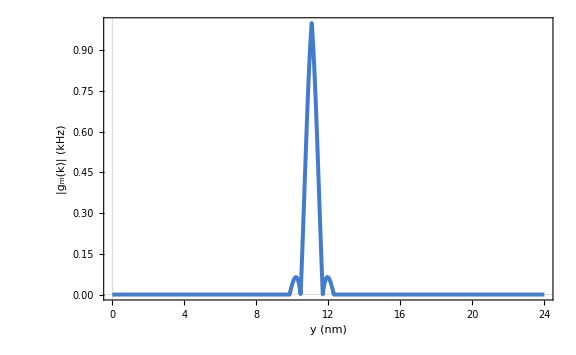

```mathematica
TestEmptyList={};

Do[
AppendTo[TestEmptyList,Table[{3/2 M *a/10^-9,Abs[ImpureUMatrixB[J,J2,DM,s,κ,h,ϕ,0.8,Num][[1]][[M]]]^2},{M,1,2Num}][[j]][[2]]]
,{j,1,Length[Table[{3/2 M *a/10^-9,Abs[ImpureUMatrixB[J,J2,DM,s,κ,h,ϕ,0.2,Num][[1]][[M]]]^2},{M,1,2Num}]]}];


v2=ListInterpolation[TestEmptyList,{0,24}];
Plot[Abs[v2[x]],{x,0,24},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[ColorData["Rainbow",1/Length[Wavefunctions]],Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

```mathematica
Export["C:\\Users\\jeffc\\Downloads\\MZNR-impure_zero_mode.png",%90,"PNG"]
```

C:\Users\jeffc\Downloads\MZNR-impure_zero_mode.png

### Coupling

```mathematica
MZNRCouplingBImpure[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,EmptyList},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
z1=0;
y1=3/2 M; 

U=ImpureUMatrixB[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[(U[[m]][[M]](1+(-1)^(M-1))/2+E^(ⅈ ξ (√3)/2)U[[m]][[M]](1+(-1)^M)/2)(A[[1]][[1]]-A[[2]][[2]])*(√3 3)/4 E^(ⅈ ξ x1),{x1,-√3*100,√3*100,√3},{M,1,2N}],{z1,-1,0},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
g
]
```

```mathematica
κ=0.22;
NSteps=80;
Num=20;
ω=2.7;
error=0.01;

l=3/2*2*Num*a;
d=8;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

CouplingList={};

Do[
numba=MeanMom[ω,error][[j]][[1]];
mom=MeanMom[ω,error][[j]][[2]];
Do[
y=-10+l*N[80/NSteps];
gy=F*(MZNRCouplingBImpure[J,J2,DM,s,κ,h,ϕ,mom,Num,numba,0,y,d]);
gm[y]={0.4*y,gy};
,{l,0,NSteps}];

AppendTo[CouplingList,Table[gm[y],{y,-10,l/a+10,N[80/NSteps]}]];

,{j,1,Length[MeanMom[ω,error]]}];
```

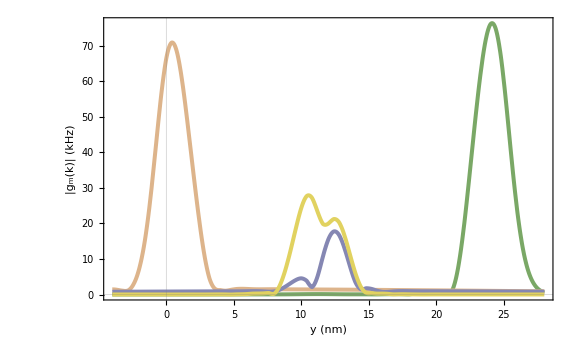

```mathematica
(*Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[ColorData["DarkBands",j/Length[Wavefunctions]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All]*)

TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,CouplingList[[i]][[j]][[2]]]
,{j,1,Length[CouplingList[[i]]]}];
,{i,1,Length[CouplingList]}];

Do[
v=ListInterpolation[TestEmptyList[[Length[CouplingList[[j]]]*(j-1)+1;;Length[CouplingList[[j]]]*j]],{-4,28}];
plot[j]=Plot[v[x],{x,-4,28},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[ColorData["DarkBands",j/Length[CouplingList]],Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[CouplingList]}];

Show[Table[plot[j],{j,1,Length[CouplingList]}],(*,pristine1,pristine2,*)ImageSize->Large,PlotRange->All]
```

# Workspace

```mathematica
0.4*RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2Num}]
```

{0.,0.2,0.6,0.8,1.2,1.4,1.8,2.,2.4,2.6,3.,3.2,3.6,3.8,4.2,4.4,4.8,5.,5.4,5.6,6.,6.2,6.6,6.8,7.2,7.4,7.8,8.,8.4,8.6,9.,9.2,9.6,9.8,10.2,10.4,10.8,11.,11.4,11.6,12.,12.2,12.6,12.8,13.2,13.4,13.8,14.,14.4,14.6,15.,15.2,15.6,15.8,16.2,16.4,16.8,17.,17.4,17.6,18.,18.2,18.6,18.8,19.2,19.4,19.8,20.,20.4,20.6,21.,21.2,21.6,21.8,22.2,22.4,22.8,23.,23.4,23.6}

```mathematica
Sum[M KroneckerDelta[Mod[M,4],1],{M,1,20}]
Sum[M,{M,1,20,4}]
```

45

45

```mathematica
KroneckerDelta[Mod[M,4],1]
```

```mathematica
F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,k,Num,numba,0,23.3/0.4,d,-√3*200,√3*200]
F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,k,Num,numba,(√3)/2,23.3/0.4,d,-√3*200,√3*200]
F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,k,Num,numba,√3,23.3/0.4,d,-√3*200,√3*200]
```

325.673

325.68

325.699

```mathematica
F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,MeanMom[3.2,0.01][[2]][[2]],Num,MeanMom[3.2,0.01][[2]][[1]],0,0,d,-√3*100,√3*100]
F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,MeanMom[3.2,0.01][[2]][[2]],Num,MeanMom[3.2,0.01][[2]][[1]],(√3)/4,0,d,-√3*100,√3*100]
F*MZNRCouplingDiscreteTest[J,J2,DM,s,κ,h,ϕ,MeanMom[3.2,0.01][[2]][[2]],Num,MeanMom[3.2,0.01][[2]][[1]],(√3)/2,0,d,-√3*100,√3*100]
```

277.566

277.557

277.533

```mathematica
test2={{{1,2},{2,3},{3,4}},{{1,2},{2,3},{3,4}}};
test2[1]
```

{{{1,2},{2,3},{3,4}},{{1,2},{2,3},{3,4}}}[1]

```mathematica
MeanMom[2.5,0.01]
```

{{21,1.34826,2.50023},{21,1.23943,2.50034},{22,1.3664,2.49862},{22,-1.39058,2.49805}}

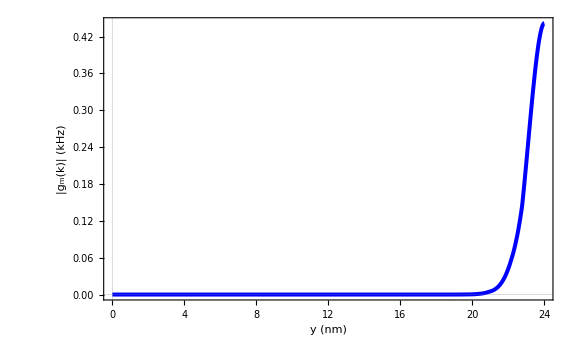

{3/5,2.9001×10^-20}

```mathematica
TestEmptyList={};
Do[
AppendTo[TestEmptyList,Wavefunctions[[1]][[j]][[2]]]
,{j,1,Length[Wavefunctions[[1]]]}];

v=ListInterpolation[TestEmptyList,{0,24}];
p4=Plot[v[x],{x,0,24},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Blue,Thickness[.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

```mathematica
Nearest[Table[f[ξ][[BandIndices[[1]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],2.7]
```

{2.51439}

```mathematica
FindMom[2.3,0.01];
Sort[FindMom[2.3,0.01],Abs[#1[[1]]]<Abs[#2[[1]]]&];
MeanMom[2.5,0.005]
```

{{31,1.23943,2.5007},{31,1.34826,2.50085},{32,1.3664,2.49862}}

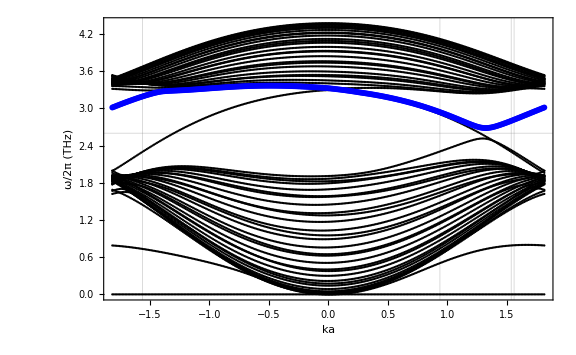

```mathematica
p=ListPlot[Table[f[ξ],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Black,Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"];
p1=ListPlot[Table[f[ξ][[33]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Blue,Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"];
Show[p,p1,PlotRange->All,ImageSize->Large,GridLines->{{1.5356834617183048,-1.5598674532414276,1.5598674532414274,0.9371296715210127},{2.6}}]
```

```mathematica
Mean[Split[FindMom[2.5,0.005],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&][[4]]]
```

{32,-1.39058,2.49805}

```mathematica
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[2.5,0.005],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList],i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];
```

```mathematica
MeanList[List_]:=
Module[{EmptyList},
EmptyList={};

]
EvenQ[1]
```

False

```mathematica
MeanMom[2.5,0.005]
DeleteDuplicates[ReplacePart[FindMom[2.5,0.005],Mean[FindMom[2.5,0.01][[{1,2}]]],{{1},{2}}]]
Sort[FindMom[2.5,0.005],Abs[#1[[1]]]<Abs[#2[[1]]]&]
```

{{31,1.23943,2.5007},{31,1.34826,2.50085},{32,1.3664,2.49862}}

{{31,1.22734,2.49523},{31,1.34221,2.50392},{31,1.3543,2.49778},{32,1.3664,2.49862},{32,-1.39058,2.49805}}

{{31,1.3543,2.49778},{31,1.34221,2.50392},{31,1.24548,2.50328},{31,1.23338,2.49813},{32,-1.39058,2.49805},{32,1.3664,2.49862}}

```mathematica
test=Delete[FindMom[2.5,0.005],{{1},{2}}]
```

{{31,1.34221,2.50392},{31,1.3543,2.49778},{32,1.3664,2.49862},{32,-1.39058,2.49805}}

```mathematica
FindMom[2.5,0.005][[1]][[1]]==FindMom[2.5,0.005][[2]][[1]]
```

True

```mathematica
MeanMom[ω_,err_]:=
Module[{MomList},
MomList=Sort[FindMom[ω,err],Abs[#1[[1]]]<Abs[#2[[1]]]&];

(*Do[
If[Abs[MomList[[i]][[2]]-MomList[[i+1]][[2]]]<0.05&&MomList[[i]][[1]]==MomList[[i+1]][[1]],DeleteElements[MomList,{MomList[[i]],MomList[[i+1]]}]&&AppendTo[MomList,{MomList[[i]][[1]],(MomList[[i]][[2]]+MomList[[i+1]][[2]])/2}]]
,{i,1,Length[FindMom[ω,err]]-1}];*)

For[i=1,i<Length[MomList]-1,i++,If[Abs[MomList[[i]][[2]]-MomList[[i+1]][[2]]]<0.05&&MomList[[i]][[1]]==MomList[[i+1]][[1]],ReplacePart[MomList,{{i},{i+1}}->{MomList[[i]][[1]],(MomList[[i]][[2]]+MomList[[i+1]][[2]])/2}]&&DeleteDuplicates[MomList]]];

DeleteDuplicates[MomList]
];
```

```mathematica
MeanMom[2.3,0.01]
FindMom[2.3,0.01]
```

{{31,-1.55987},{31,-1.02782},{31,-1.01573},{31,-1.00364},{32,-1.62033},{32,-1.60824},{32,1.53568}}

{{31,-1.00364},{31,-1.01573},{31,-1.02782},{32,1.53568},{31,-1.55987},{32,-1.60824},{32,-1.62033}}

```mathematica
ReplacePart[MeanMom[2.3,0.01],{{1},{2}}->{1,2}]
```

{{1,2},{1,2},{31,-1.02177},{31,-1.02177},{31,-1.02177},{32,-1.61428},{32,-1.61428},{32,-1.61428},{32,-1.61428}}

```mathematica
Sort[FindMom[2.3,0.01],Abs[#1[[1]]]<Abs[#2[[1]]]&]
```

{{31,-1.0127},{31,-1.02177},{31,-1.02177},{31,-1.02177},{31,-1.02177},{32,-1.61428},{32,-1.61428},{32,-1.61428},{32,-1.61428}}

```mathematica
Abs[FindMom[2.3,0.01][[1]][[2]]-FindMom[2.3,0.01][[1+1]][[2]]]<0.05&&FindMom[2.3,0.01][[1]][[1]]==FindMom[2.3,0.01][[1+1]][[1]]
```

True

```mathematica
FindMom[2.3,0.01]=DeleteElements[FindMom[2.3,0.01],{FindMom[2.3,0.01][[1]],FindMom[2.3,0.01][[2]]}]
FindMom[2.3,0.01]
```

{{31,-1.02177},{32,-1.61428},{31,-1.02177},{32,-1.61428},{31,-1.02177},{32,-1.61428},{31,-1.02177},{32,-1.61428},{31,-1.0127}}

{{31,-1.02177},{32,-1.61428},{31,-1.02177},{32,-1.61428},{31,-1.02177},{32,-1.61428},{31,-1.02177},{32,-1.61428},{31,-1.0127}}

```mathematica
κ=0.22;
NSteps=50;
Num=50;

l=3/2*2*Num*a;
d=5;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3 (*kHz*)
```

156.514

```mathematica
MZNRCouplingTest[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
z1=0;
y1=3/2 M;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[(U[[m]][[M]](1+(-1)^(M-1))/2+E^(ⅈ ξ (√3)/2)U[[m]][[M]](1+(-1)^M)/2)*(A[[1]][[1]]+A[[2]][[2]])*(√3 3)/4 E^(ⅈ ξ x1),{x1,-√3*100,√3*100,√3},{M,1,2N}],{z1,-1/10,0},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->16,AccuracyGoal->16]];
g
]
```

```mathematica
MZNRCouplingTest[J,J2,DM,s,κ,h,ϕ,1.2153,Num,Num+1,0,150,d]
```

0.000150389

```mathematica
MZNRCouplingTest[J,J2,DM,s,κ,h,ϕ,1.2153,30,31,0,150,d]
```

8.61892×10^-9

```mathematica
MZNRCouplingTest2[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
y1=0;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[(A[[1]][[1]]+A[[2]][[2]])*(√3 3)/4 E^(ⅈ ξ x1),{x1,-√3*100,√3*100,√3}],{z1,-1/10,0},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->16,AccuracyGoal->16]];
g
]
```

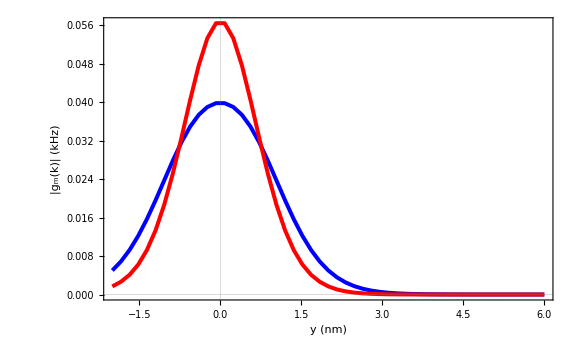

```mathematica
κ=0.22;
NSteps=50;
Num=30;

l=3/2*2*Num*a;
d=5;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3; (*kHz*)


Quiet[
Do[
y=-5+j*N[20/NSteps];
(*FIXED ENERGY*)
gy=F*(MZNRCouplingTest2[J,J2,DM,s,κ,h,ϕ,1.2153,Num,Num+1,0,y,d]);
(*MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num,0,y,d]*)
gm[y]={0.4*y,gy};
,{j,0,NSteps}];

];

cplot2=ListPlot[Table[gm[y],{y,-5,15,N[20/NSteps]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotRange->All,PlotTheme->"Scientific",Joined-> True];

Show[cplot,cplot2,PlotRange->All,ImageSize->Large]
```

```mathematica
Integrate[x1 Sum[DiracDelta[x1-√3 m],{m,0,50,1}],{x1,-1000,1000}]
```

1275 √3

```mathematica
MZNRCouplingTest[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
y1=3/2 M;
U=UMatrix[J1,J2,DM,s,κ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[(U[[m]][[M]](1+(-1)^(M-1))/2+E^(ⅈ ξ Indexed[δ,3].{1,0})U[[m]][[M]](1+(-1)^M)/2)(A[[1]][[1]]+A[[2]][[2]])*3/2 E^(ⅈ ξ x1),{x1,-√3*200,√3*200,√3},{M,1,2N}],{z1,-1,0}]];
g
]
```

```mathematica
MZNRCouplingTest[J,J2,DMI,S,κ,h03,ϕ,1.2153,Num,Num+1,0,150,d]
```

0.0815761

```mathematica
MZNRCoupling[J,J2,DMI,S,κ,h03,ϕ,1.2153,Num,Num+1,0,150,d]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.121239

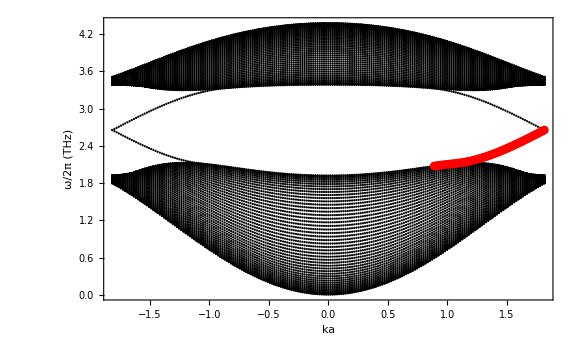

```mathematica
Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}][[150;;201]];
p3=ListPlot[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}][[150;;201]],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Red,Thickness[.001]],PlotRange->All,PlotTheme->"Scientific"];
Show[{p,p3},ImageSize->Large,PlotRange->All,GridLines->{{},{}}]
```

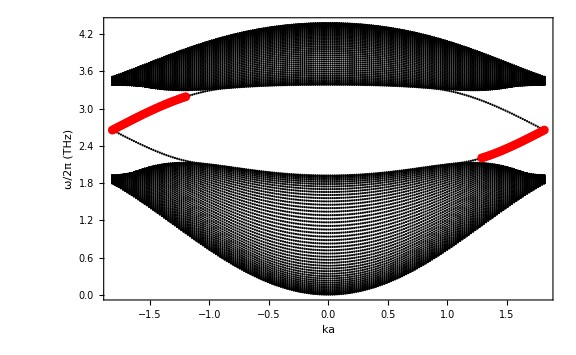

```mathematica
Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}];
Select[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],{#[[1]]>0&,#[[2]]>2.2&}];
(*p4=ListPlot[Select[Join[Select[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],#[[1]]>0&],Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}]],#[[1]]<0&],3.2>#[[2]]>2.2&],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Red,Thickness[.001]],PlotRange->All,PlotTheme->"Scientific"];*)
RightBand=Select[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],#[[1]]>0&];
LeftBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],#[[1]]<0&];
p5=ListPlot[Select[Join[RightBand,LeftBand],2.2<#[[2]]<3.2&],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω/2π (THz)"},PlotStyle->Directive[Red,Thickness[.001]],PlotRange->All,PlotTheme->"Scientific"];
Show[{p,p5},ImageSize->Large,PlotRange->All,GridLines->{{},{}}]
```

```mathematica
Select[Select[Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],#[[1]]>0&],#[[2]]>2.2&]
```

{{0.018138,3.38501},{0.036276,3.38497},{0.054414,3.38489},{0.072552,3.38479},{0.09069,3.38465},{0.108828,3.38448},{0.126966,3.38428},{0.145104,3.38405},{0.163242,3.38378},{0.18138,3.38347},{0.199518,3.38313},{0.217656,3.38275},{0.235794,3.38232},{0.253932,3.38185},{0.27207,3.38134},{0.290208,3.38077},{0.308346,3.38016},{0.326484,3.3795},{0.344622,3.37878},{0.36276,3.378},{0.380898,3.37717},{0.399036,3.37627},{0.417174,3.37532},{0.435312,3.37429},{0.45345,3.3732},{0.471588,3.37205},{0.489726,3.37082},{0.507864,3.36952},{0.526002,3.36814},{0.54414,3.3667},{0.562278,3.36517},{0.580416,3.36358},{0.598554,3.3619},{0.616692,3.36015},{0.63483,3.35832},{0.652968,3.35642},{0.671106,3.35445},{0.689244,3.3524},{0.707382,3.35028},{0.72552,3.34809},{0.743658,3.34583},{0.761796,3.34349},{0.779934,3.34109},{0.798072,3.3386},{0.81621,3.33601},{0.834348,3.33328},{0.852486,3.33034},{0.870624,3.32708},{0.888762,3.32339},{0.9069,3.31924},{0.925038,3.3146},{0.943176,3.30948},{0.961314,3.30389},{0.979452,3.29783},{0.99759,3.2913},{1.01573,3.28432},{1.03387,3.2769},{1.052,3.26903},{1.07014,3.26072},{1.08828,3.25199},{1.10642,3.24283},{1.12456,3.23327},{1.14269,3.22329},{1.16083,3.21292},{1.17897,3.20216},{1.19711,3.19101},{1.21525,3.17949},{1.23338,3.16761},{1.25152,3.15536},{1.26966,3.14277},{1.2878,3.12984},{1.30594,3.11658},{1.32407,3.10299},{1.34221,3.0891},{1.36035,3.0749},{1.37849,3.06041},{1.39663,3.04563},{1.41476,3.03058},{1.4329,3.01527},{1.45104,2.99971},{1.46918,2.98391},{1.48732,2.96787},{1.50545,2.95162},{1.52359,2.93516},{1.54173,2.91851},{1.55987,2.90167},{1.57801,2.88466},{1.59614,2.86749},{1.61428,2.85018},{1.63242,2.83272},{1.65056,2.81515},{1.6687,2.79747},{1.68683,2.7797},{1.70497,2.76184},{1.72311,2.74392},{1.74125,2.72594},{1.75939,2.70793},{1.77752,2.68989},{1.79566,2.67184},{1.8138,2.65379}}

```mathematica
Join[Table[f[ξ][[Num]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}],Table[f[ξ][[Num+1]],{ξ,-Pi/(√3),Pi/(√3),N[((2Pi)/(√3))/Naux]}]];
```

```mathematica
(*G=1/(√((x-x1)^2+(y-y1)^2+(z-z1)^2));
DG=({{D[D[G,x1],x], D[D[G,y1],x], D[D[G,z1],x]}, {D[D[G,x1],y], D[D[G,y1],y], D[D[G,z1],y]}, {D[D[G,x1],z], D[D[G,y1],z], D[D[G,z1],z]}});*)
MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num+1,0,0,d]+MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.6,Num,Num+1,0,0,d]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

MaxValue::ivar: 18.3333 is not a valid variable.

MaxValue[8.55173×10^-10,18.3333]

```mathematica
Num=50;
l=(√3)/2 2*Num*a;
w=10^-11;(*m*)
d=5;
F=γe*μ0*√((3μB Ms)/(2l w))*10^3; (*KHz*)
N[l]*10^9
```

34.641

```mathematica
Clear[x,y,z];
A=DyadG[x,y,z,x1,y1,z1];
x=0;
y=0;
z=d;
A[[1]][[1]]+A[[2]][[2]]
```

-(3 x1^2)/((x1^2+y1^2+(5-z1)^2)^(5/2))-(3 y1^2)/((x1^2+y1^2+(5-z1)^2)^(5/2))+2/((x1^2+y1^2+(5-z1)^2)^(3/2))

$Aborted

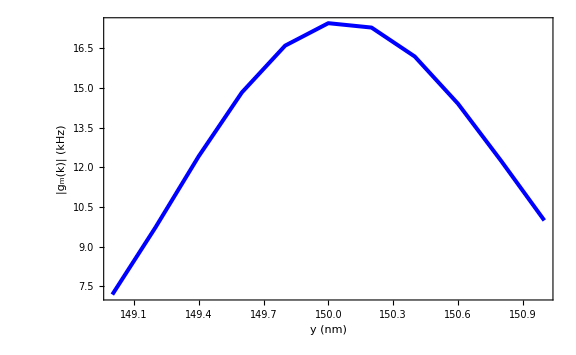

$Aborted

```mathematica
NSteps=10;

Num=50;
l=3/2*2*Num*a;
d=2;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3; (*KHz*)


Quiet[
Do[
y=149+j*N[2/NSteps];
(*FIXED ENERGY*)
gy=F*((*MZNRCoupling[J,J2,DM,s,κ,h,ϕ,-1.5,Num,Num,0,y,d]*)MZNRCoupling[J,J2,DM,s,κ,h,ϕ,1.6,Num,Num+1,0,y,d]);
gm[y]={y,gy};
,{j,0,NSteps}];

];
cplot=ListPlot[Table[gm[y],{y,149,151,N[2/NSteps]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Blue,Thickness[.005]],PlotRange->All,PlotTheme->"Scientific",Joined-> True];

Show[cplot,PlotRange->All,ImageSize->Large]
```